### Option pricing functions - Normal - definitions

```mathematica
nn[x_,μ_:0,σ_:1]:=(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ);
NN[x_,μ_:0,σ_:1]:=1/2 Erfc[(-x+μ)/(√2 σ)];
NNInv[y_,μ_:0,σ_:1]:=μ-√2 σ InverseErfc[2 y];
```

```mathematica
Solve[NN[x,μ,σ]==y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→μ-√2 σ InverseErfc[2 y]}}

#### Option pricing functions - Normal - expected behavior

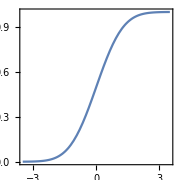

```mathematica
Plot[1/2 Erfc[-x/(√2)],{x,-3.5,+3.5},AspectRatio->1,Frame->True,AxesOrigin->{0,1/2},ImageSize->Small]
```

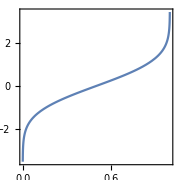

```mathematica
Plot[-√2  InverseErfc[2 y],{y,0,1},AspectRatio->1,Frame->True,AxesOrigin->{1/2,0},ImageSize->Small]
```

```mathematica
{nn[-∞]==0,nn[+∞]==0,NN[-∞]==0,NN[+∞]==1}
```

{True,True,True,True}

### Option pricing functions - d1, d2 - definitions

```mathematica
dd1[x_,K_,σ_,τ_]:=If[τ==0,If[x==K,0,Sign[Log[x/K]]Infinity],(Log[x/K]+(σ^2τ)/2)/(σ Sqrt[τ])];
dd1::usage="dd1[x,K,σ,τ] returns d1 for the price x, the strike K, volatility σ and time to expiry τ";
dd2[x_,K_,σ_,τ_]:=If[τ==0,If[x==K,0,Sign[Log[x/K]]Infinity],(Log[x/K]-(σ^2τ)/2)/(σ Sqrt[τ])];
dd2::usage="dd2[x,K,σ,τ] returns d2 for the price x, the strike K, volatility σ and time to expiry τ";
```

d_(1,2)=(Log[x/K]±(σ^2 τ)/2)/(σ √τ)

#### Option pricing functions - d1, d2 - expected behavior

```mathematica
Assuming[K>0&&x==K&&σ>0,Limit[(Log[x/K]+(σ^2τ)/2)/(σ Sqrt[τ]),τ->0]]
```

0

```mathematica
Refine[{dd1[0.5K,K,σ,0],dd1[K,K,σ,0],dd1[2K,K,σ,0]},K>0]
```

{-∞,0,∞}

```mathematica
Refine[{dd2[0.5K,K,σ,0],dd2[K,K,σ,0],dd2[2K,K,σ,0]},K>0]
```

{-∞,0,∞}

```mathematica
Refine[{NN[dd1[0.5K,K,σ,0]],NN[dd1[K,K,σ,0]],NN[dd1[2K,K,σ,0]]},K>0]
```

{0,1/2,1}

### B&S Option pricing functions - premium, greeks - Definitions

```mathematica
bspremium[ϕ_,S_,K_,r_,q_,σ_,τ_] :=ϕ S Exp[-q τ] NN [ϕ dd1[S Exp[(r-q)τ],K,σ,τ]] - ϕ K Exp[-r τ]NN [ϕ dd2[S Exp[(r-q)τ],K,σ,τ]];
bspremium::usage="bspremium[ϕ,S,K,r,q,σ,τ] returns the B&S premium for a call (ϕ=1) or a put(ϕ=-1)";
bsdelta[ϕ_,S_,K_,r_,q_,σ_,τ_] := ϕ Exp[-q τ]NN [ϕ  dd1[S Exp[(r-q)τ],K,σ,τ]];
bsdelta::usage="bsdelta[ϕ,S,K,r,q,σ,τ] returns the B&S delta for a call (ϕ=1) or a put(ϕ=-1)";
bsgamma [S_,K_,r_,q_,σ_,τ_] :=If[τ==0,DiracDelta[S-K],If[τ>0,Exp[-q τ]nn [ dd1[S Exp[(r-q)τ],K,σ,τ]]/(σ S Sqrt[τ])]];
bsgamma::usage="bsgamma[S,K,r,q,σ,τ] returns the B&S gamma for a call or a put";
bsvega [S_,K_,r_,q_,σ_,τ_] := S Exp[-q τ] Sqrt[τ] nn [ dd1[S Exp[(r-q)τ],K,σ,τ]];
bsvega::usage="bsvega[S,K,r,q,σ,τ] returns the B&S vega for a call or a put";
bstheta [ϕ_,S_,K_,r_,q_,σ_,τ_] :=If[τ<=0,0,-S σ Exp[-q τ]  nn [ dd1[S Exp[(r-q)τ],K,σ,τ]]/(2 Sqrt[τ] )+q S ϕ Exp[-q τ] NN [ϕ dd1[S Exp[(r-q)τ],K,σ,τ]]-r K ϕ Exp[-r τ]NN [ϕ  dd2[S Exp[(r-q)τ],K,σ,τ]]];
bstheta::usage="bstheta[ϕ,S,K,r,q,σ,τ] returns the B&S theta for a call or a put";
bsvanna[S_,K_,r_,q_,σ_,τ_]:=- Exp[-q τ]nn [ dd1[S Exp[(r-q)τ],K,σ,τ]]  dd2[S Exp[(r-q)τ],K,σ,τ]/σ;
bsvanna::usage="bsvanna[S,K,r,q,σ,τ] returns the vanna (∂_σ  delta) for a call or a put";
bsvolga[S_,K_,r_,q_,σ_,τ_]:=Exp[-q τ] S Sqrt[τ]nn [ dd1[S Exp[(r-q)τ],K,σ,τ]] dd1[S Exp[(r-q)τ],K,σ,τ] dd2[S Exp[(r-q)τ],K,σ,τ]/σ;
bsvolga::usage="bsvolga[S,K,r,q,σ,τ] returns the volga/gov (∂_σ  vega) for a call or a put";
bsimpliedvol[ϕ_,S_,K_,r_,q_,p_,τ_] := σ/.FindRoot[bspremium[ϕ,S,K,r,q,σ,τ]==p ,{σ,0.2}];
bsimpliedvol::usage="bsimpliedvol[ϕ,S,K,r,q,p,τ] returns the B&S implied vol for a call (ϕ=1) or a put(ϕ=-1) given a premium p";
strikedelta[ϕ_,S_,r_,q_,σ_,τ_,δ_]:=FindRoot[bsdelta[ϕ,S,K,r,q,σ,τ]==δ,{K,S}]⟦1,2⟧; 
strikedelta::usage="strikedelta[ϕ,S,r,q,σ,τ,δ] returns the strike for a given delta for a call (ϕ=1) or a put(ϕ=-1)";
```

#### B&S Option pricing functions - premium, greeks - Expected behavior

```mathematica
vanilla[ϕ_,S_,K_,r_,q_,σ_,τ_,prop_:"Value"]:=FinancialDerivative[{"European",If[ϕ==1,"Call","Put"]}, {"StrikePrice"->K, "Expiration"->τ},  { "CurrentPrice"-> S, "Volatility" -> σ,"InterestRate"-> r, "Dividend"->q},{prop}];
```

```mathematica
vanillaIV[ϕ_,S_,K_,r_,q_,opt_,τ_]:=FinancialDerivative[{"European",If[ϕ==1,"Call","Put"]}, {"StrikePrice"->K, "Expiration"->τ},  { "CurrentPrice"-> S, "Value" -> opt,"Value"-> opt,"InterestRate"-> r, "Dividend"->q},{"ImpliedVolatility"}];
```

```mathematica
{vanilla[1,100,100,0,0,0.20,1],vanilla[1,100,100,0,0,0.20,1,"Delta"],vanilla[1,100,100,0,0,0.20,1,"Gamma"],vanilla[1,100,100,0,0,0.20,1,"Vega"],vanilla[1,100,100,0,0,0.20,1,"Theta"],vanilla[1,100,100,0,0,0.20,1,"Rho"]}
```

{7.96557,0.539827,0.0198477,39.6953,-3.9693,46.0172}

```mathematica
vanillaIV[1,100,100,0,0,8,1]
```

0.200867

```mathematica
{bspremium[1,100,100,0,0,0.20,1],bsdelta[1,100,100,0,0,0.20,1],bsgamma[100,100,0,0,0.20,1],bsvega[100,100,0,0,0.20,1],bstheta[1,100,100,0,0,0.20,1],bsvanna[100,100,0,0,0.20,1],bsvolga[100,100,0,0,0.20,1]}
```

{7.96557,0.539828,0.0198476,39.6953,-3.96953,0.198476,-1.98476}

```mathematica
bsimpliedvol[1,100,100,0,0,8,1]
```

0.200867

```mathematica
Plot3D[bspremium[1,S,100,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[vanilla[1,S,100,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[bsdelta[1,S,100,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[vanilla[1,S,100,0,0,0.20,1-t,"Delta"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[bsgamma[S,100,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[vanilla[1,S,100,0,0,0.20,1-t,"Gamma"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[bsvega[S,100,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[vanilla[1,S,100,0,0,0.20,1-t,"Vega"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

### Binary Option pricing functions - premium

```mathematica
binarypremium[ϕ_,S_,K_,r_,q_,σ_,τ_,po_:1] :=po Exp[-r τ]NN [ ϕ dd2[S Exp[(r-q)τ],K,σ,τ]];
binarypremium::usage="binarypremium[ϕ,S,K,r,q,σ,τ,po] returns the premium for an european binary cash-or-nothing call (ϕ=1) or a put(ϕ=-1) that pays po in case of exercise";
```

#### Binary Option pricing functions - Expected Behavior

```mathematica
binary[ϕ_,S_,K_,r_,q_,σ_,τ_,prop_:"Value"]:=FinancialDerivative[{"BinaryCash","European",If[ϕ==1,"Call","Put"]}, {"StrikePrice"->K, "Expiration"->τ},  { "CurrentPrice"-> S, "Volatility" -> σ,"InterestRate"-> r, "Dividend"->q},{prop}];
```

```mathematica
{binary[1,100,100,0,0,0.20,1],binary[1,100,100,0,0,0.20,1,"Delta"],binary[1,100,100,0,0,0.20,1,"Gamma"],binary[1,100,100,0,0,0.20,1,"Vega"],binary[1,100,100,0,0,0.20,1,"Theta"],binary[1,100,100,0,0,0.20,1,"Rho"]}
```

{0.460172,0.0198476,-0.0000992383,-0.198476,0.0198476,1.52459}

```mathematica
binarypremium[1,100,100,0,0,0.20,1]
```

0.460172

```mathematica
Plot3D[binary[1,S,100,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[binary[1,S,100,0,0,0.20,1-t,"Delta"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[binary[1,S,100,0,0,0.20,1-t,"Gamma"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[binary[1,S,100,0,0,0.20,1-t,"Vega"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

### OT Option pricing functions - premium

```mathematica
onetouchpremium[lh_,po_,ph_,S_,H_,r_,q_,σ_,τ_]:=po Exp[-ph r τ] Min[1,(H/S)^(-1/2+((r-q)+Sqrt[(r-q-σ^2/2)^2+2 (1-ph)r σ^2])/σ^2)NN[lh (Log[H/S]+τ Sqrt[(r-q-σ^2/2)^2+2 (1-ph)r σ^2])/(σ Sqrt[τ])]+
(H/S)^(-1/2+((r-q)-Sqrt[(r-q-σ^2/2)^2+2 (1-ph)r σ^2])/σ^2)NN[lh (Log[H/S]-τ Sqrt[(r-q-σ^2/2)^2+2 (1-ph)r σ^2])/(σ Sqrt[τ])]];
onetouchpremium::usage="onetouchpremium[lh,po,ph,S,H,r,q,σ,τ] returns the premium for an one-touch (aka american binary cash-or-nothing) put (lh=1) or a call (lh=-1); lh = low barrier or high barrier that pays po immediately (ph=0) or at expiry (ph=1) in case of exercise (hitting the barrier H)";
```

```mathematica
onetouch[ϕ_,S_,K_,r_,q_,σ_,τ_,prop_:"Value"]:=FinancialDerivative[{"OneTouch","American",If[ϕ==1,"Call","Put"]}, {"StrikePrice"->K, "Expiration"->τ},  { "CurrentPrice"-> S, "Volatility" -> σ,"InterestRate"-> r, "Dividend"->q},{prop}];
```

```mathematica
{onetouch[1,100,110,0,0,0.20,1],onetouch[1,100,110,0,0,0.20,1,"Delta"],onetouch[1,100,110,0,0,0.20,1,"Gamma"],onetouch[1,100,110,0,0,0.20,1,"Vega"],onetouch[1,100,110,0,0,0.20,1,"Theta"],onetouch[1,100,110,0,0,0.20,1,"Rho"]}
```

{0.603261,0.0369967,0.000805025,1.61004,-0.161004,1.34445}

```mathematica
onetouchpremium[-1,1,0,100,110,0,0,0.20,1]
```

0.603261

```mathematica
{onetouch[1,100,110,0.10,0,0.20,1]}
```

{0.726029}

```mathematica
onetouchpremium[-1,1,0,100,110,0.10,0,0.20,1]
```

0.726029

```mathematica
Plot3D[onetouch[1,S,110,0,0,0.20,1-t],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[onetouch[1,S,110,0,0,0.20,1-t,"Delta"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[onetouch[1,S,110,0,0,0.20,1-t,"Gamma"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[onetouch[1,S,110,0,0,0.20,1-t,"Vega"],{S,80,125},{t,0,1},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

### DNT Option pricing functions - premium

```mathematica
doublenotouchpremium[S_,LB_,UB_,r_,q_,σ_,τ_,jn_:20,po_:1]:=If[S≤LB,0,
If[S≥UB,0,Sum[((2π j po)/Log[UB/LB]^2)(((S/LB)^(-1/2((2(r-q))/σ^2-1))-(-1)^j(S/UB)^(-1/2((2(r-q))/σ^2-1)))/((-1/2((2(r-q))/σ^2-1))^2+((j π)/Log[UB/LB])^2))
Sin[((j π)/Log[UB/LB] Log[S/LB])] ⅇ^(-1/2(((j π)/Log[UB/LB])^2-(-1/4((2(r-q))/σ^2-1)^2-2 r/σ^2))σ^2 τ),{j,1,jn}]]];
doublenotouchpremium::usage="doublenotouchpremium[po,S,LB,UB,r,q,σ,τ,jn]
 returns the premium for a double-no-touch calculated as the sum of a series of jn terms";
```

```mathematica
pdesolut[boundcond_,τ_,σ_,r_,q_,LB_,UB_]:=NDSolve[Prepend[boundcond,
D[C[S,t],t]+1/2 S^2 σ^2 D[C[S,t],{S,2}]+(r-q)S D[C[S,t],S]-r C[S,t]==0]
,C,{S,LB,UB},{t,0,τ},AccuracyGoal->6,PrecisionGoal->6]⟦1,1,2⟧;
pdesolut::usage="pdesolut[boundcond,τ,σ,r,q,LB,UB] returns an interpolating function C[S,t]
 as the solution of the BS PDE, given a set of boundary conditions and the parameters σ, r, q";
```

```mathematica
dntpdesolut[LB_,UB_,r_,q_,σ_,τ_,po_:1,poR_:0]:=pdesolut[{C[S,τ]==If[LB<S<UB,po,poR],
C[LB,t]==poR Exp[-(r)(τ-t)],C[UB,t]==poR Exp[-(r)(τ-t)]},τ,σ,r,q,LB,UB];
dntpdesolut::usage="dntpdesolut[po,poR,LB,UB,r,q,τ,σ] returns an interpolating function C[S,t]
 as the solution of the BS PDE for a DNT, given the set of boundary conditions and the parameters σ, r, q";
```

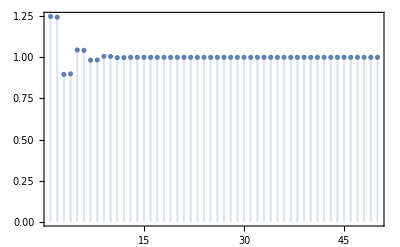

```mathematica
DiscretePlot[doublenotouchpremium[100,90,110,0,0,0.20,1/252,jn],{jn,1,50},Frame->True,PlotRange->{All,{0,Automatic}}]
```

```mathematica
doublenotouchpremium[100,90,110,0,0,0.20,1/4,100]
```

General::munfl: 2.78161×10^-307 7.12807×10^-7 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-765.919] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-828.417] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.373209

```mathematica
DNT901103m=dntpdesolut[90,110,0,0,0.20,1/4];
```

```mathematica
DNT901103m[100,0]
```

0.373208

```mathematica
Plot3D[doublenotouchpremium[S,90,110,0,0,0.20,1/4-t,100],{S,90,110},{t,0,1/4},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&),PlotRange->All]
```

General::munfl: 4.03703×10^-9 2.9256×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-765.864] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-828.358] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[DNT901103m[S,1/4-t],{S,90,110},{t,0,1/4},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&),PlotRange->All]
```

-Graphics3D-

### RKO Option pricing functions - premium

```mathematica
rkouppdesolut[K_,LB_,UB_,r_,q_,σ_,τ_,po_:10]:=pdesolut[{C[S,τ]==If[K<S<UB,Max[S-K,0],0],
C[LB,t]==0,C[UB,t]==0},τ,σ,r,q,LB,UB];
rkouppdesolut::usage="rkouppdesolut[K,LB,UB,r,q,τ,σ] returns an interpolating function C[S,t]
 as the solution of the BS PDE for a RKO Up, given K and the barriers, the set of boundary conditions and the parameters σ, r, q";
```

```mathematica
RKOUpEUR=rkouppdesolut[1.19,1.10,1.2055,0.0012,-0.00557,0.0511,26/365];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable S.

```mathematica
RKOUpEUR[1.1872,0]400
```

0.41697

```mathematica
Show[Plot3D[RKOUpEUR[S,(26-d)/365]400,{S,1.17,1.2055},{d,0,26},ImageSize->Medium,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&),PlotRange->All,ImageSize->Large],
ListPointPlot3D[{{1.1872,26,RKOUpEUR[1.1872,0]400}},PlotStyle->Black]]
```

-Graphics3D-

### FX Smile interpolation - mkt

```mathematica
volsfromparam5[atm_,rr25_,st25_,rr10_,st10_]:={atm-rr10/2+st10,atm-rr25/2+st25,atm,atm+rr25/2+st25,atm+rr10/2+st10};
volsfromparam5::"usage"="volsfromparam5[atm,rr25,st25,rr10,st10] returns the vols for {p10d,p25d,atm,c25d,c10d}";
paramfromvols[atm_,c25_,p25_,c10_,p10_]:={atm,c25-p25,(c25+p25)/2-atm,c10-p10,(c10+p10)/2-atm};
paramfromvols::"usage"="paramfromvols[atm,c25,p25,c10,p10] returns the parameters {atm,rr25,st25,rr10,st10}";
volsfrommkt[atm_,rr25_,st25_,rr10_,st10_]:={{atm,atm},{atm+rr25/2+st25,atm-rr25/2+st25},{atm+st25,atm+st25},{atm+rr10/2+st10,atm-rr10/2+st10},{atm+st10,atm+st10}};
volsfrommkt::"usage"="volsfrommkt[atm,rr25,st25,rr10,st10] returns the vols for the traded structures {atm straddle,rr25,st25,rr10,st10}";
volsfromsmlmkt[atm_,rr25_,st25_,rr10_,st10_]:={{atm,atm},{atm+st25,atm+st25},{atm+st10,atm+st10}};
volsfromsmlmkt::"usage"="volsfromsmlmkt[atm,rr25,st25,rr10,st10] returns the vols for the traded structures {atm straddle,st25,st10}";
```

```mathematica
(*
Kfromσδf[f_,σ_,δ_,τ_]:=FindRoot[-(K/f)bsdelta[Sign[δ],1/f,1/K,0,0,σ,τ]==δ,{K,f}]⟦1,2⟧;
Kfromσδf::"usage"="Kfromσδf[f,σ,δ,τ] returns the strike K for a given delta and vol (inverted quote)";
σfromδ[f_,K_,τ_,ϕ_,δ_]:=-ϕ(NNInv[(f δ)/(K ϕ)]+Sqrt[(NNInv[(f δ)/(K ϕ)])^2-2Log[K/f]])/Sqrt[τ];
σfromδ::"usage"="σfromδ[f,K,τ,δ] returns implied vol σ for a given strike and delta (inverted quote)";
*)
Kfromσδf[f_,σ_,δ_,τ_]:=FindRoot[bsdelta[Sign[δ],f,K,0,0,σ,τ]==δ,{K,f}]⟦1,2⟧;
Kfromσδf::"usage"="Kfromσδf[f,σ,δ,τ] returns the strike K for a given delta and vol";
```

```mathematica
Plot3D[Log[Kfromσδf[1,σ,0.25,τ]],{σ,0.05,0.10},{τ,1/252,10},PlotRange->All,AxesLabel->Automatic,PlotLabel->"Log[K/f] for 25Δ Call",ImageSize->Large,ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

```mathematica
years=Join[{7,14,21,31,61,92,123,153,184,275,365}/365,{1.5,2,3,4,5,6,7,10}];
```

```mathematica
DateDifference[{2019,8,5},{2020,5,5}]
```

274 days

```mathematica
years2=Join[{7,14,21,31,61,92,122,153,184,274,365}/365,{1.5,2,3,4,5,6,7,10}];
```

```mathematica
volsc25d={0.05297,0.05513,0.05803,0.06095,0.06058,0.061,0.06224,0.063,0.0634,0.06449,0.06672,0.06848,0.06928,0.07319,0.07648,0.07855,0.07993,0.08095,0.08372};
```

```mathematica
volsc25d2={6.19,6.151,5.964,5.979,6.4,6.646,6.615,6.622,6.607,6.715,6.856,7.2,7.388,7.762,8.11,8.368,8.557,8.699,8.965}/100;
```

```mathematica
volsp25d2={6.17,6.154,6.026,6.031,6.51,6.864,6.82,6.82,6.802,6.855,6.944,7.285,7.473,7.842,8.215,8.503,8.705,8.846,9.14}/100;
```

```mathematica
volsatm2={6.02,5.98,5.815,5.81,6.235,6.505,6.463,6.459,6.435,6.505,6.61,6.945,7.13,7.5,7.858,8.128,8.279,8.385,8.665}/100;
```

```mathematica
logkc25d=MapThread[Log[Kfromσδf[1,#1,0.25,#2]]&,{volsc25d,years}];
```

```mathematica
logkc25d2=MapThread[Log[Kfromσδf[1,#1,0.25,#2]]&,{volsc25d2,years2}];
```

```mathematica
logkp25d2=MapThread[Log[Kfromσδf[1,#1,-0.25,#2]]&,{volsp25d2,years2}];
```

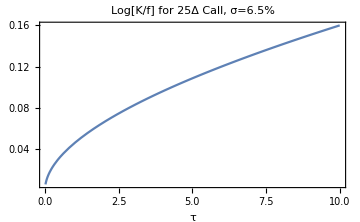

```mathematica
Plot[Log[Kfromσδf[1,0.065,0.25,τ]],{τ,7/365,10},PlotRange->All,PlotLabel->"Log[K/f] for 25Δ Call, σ=6.5%",ImageSize->Medium,Frame->True,FrameLabel->"τ"]
```

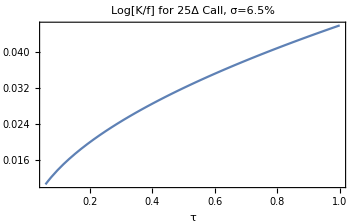

```mathematica
Plot[Log[Kfromσδf[1,0.065,0.25,τ]],{τ,21/365,1},PlotRange->All,PlotLabel->"Log[K/f] for 25Δ Call, σ=6.5%",ImageSize->Medium,Frame->True,FrameLabel->"τ"]
```

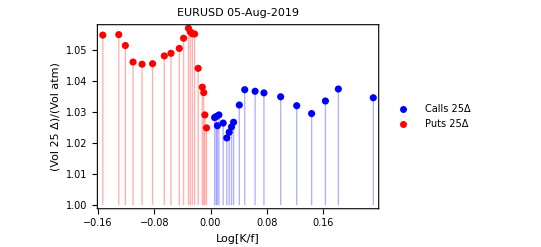

```mathematica
ListPlot[{Transpose[{logkc25d2,volsc25d2/volsatm2}],Transpose[{logkp25d2,volsp25d2/volsatm2}]},Frame->True,PlotRange->All,Filling->Axis,AxesOrigin->{0,1},PlotStyle->{Blue,Red},PlotLegends->{"Calls 25Δ","Puts 25Δ"},PlotLabel->"EURUSD 05-Aug-2019",FrameLabel->{"Log[K/f]","(Vol 25  Δ)/(Vol  atm)"}]
```

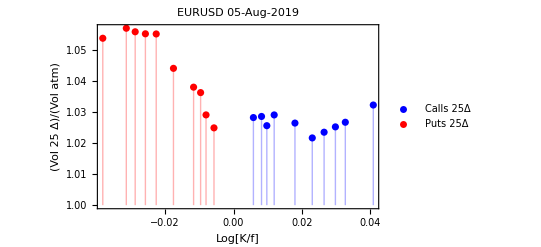

```mathematica
ListPlot[Map[Take[#,10]&,{Transpose[{logkc25d2,volsc25d2/volsatm2}],Transpose[{logkp25d2,volsp25d2/volsatm2}]}],Frame->True,PlotRange->All,Filling->Axis,AxesOrigin->{0,1},PlotStyle->{Blue,Red},PlotLegends->{"Calls 25Δ","Puts 25Δ"},PlotLabel->"EURUSD 05-Aug-2019",FrameLabel->{"Log[K/f]","(Vol 25  Δ)/(Vol  atm)"}]
```

```mathematica
pointsc25d=Transpose[{volsc25d,years,logkc25d}];
```

```mathematica
pointsc25d2=Transpose[{volsc25d2,years2,logkc25d2}];
```

```mathematica
Show[Plot3D[Log[Kfromσδf[1,σ,0.25,τ]],{σ,0.05,0.085},{τ,7/365,10},PlotRange->All,AxesLabel->Automatic,PlotLabel->"Log[K/f] for 25Δ Call - 24-May-2021",ImageSize->Large,ColorFunction->(ColorData["TemperatureMap"][#3]&)],
ListLinePlot3D[pointsc25d,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Show[Plot3D[Log[Kfromσδf[1,σ,0.25,τ]],{σ,0.05,0.09},{τ,7/365,10},PlotRange->All,AxesLabel->Automatic,PlotLabel->"Log[K/f] for 25Δ Call - 05-Aug-2019",ImageSize->Large,ColorFunction->(ColorData["TemperatureMap"][#3]&)],
ListLinePlot3D[pointsc25d2,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Show[Plot3D[Log[Kfromσδf[1,σ,0.25,τ]],{σ,0.055,0.075},{τ,7/365,1},PlotRange->All,AxesLabel->Automatic,PlotLabel->"Log[K/f] for 25Δ Call - 05-Aug-2019",ImageSize->Large,ColorFunction->(ColorData["TemperatureMap"][#3]&)],
ListLinePlot3D[Take[pointsc25d2,11],PlotStyle->Black]]
```

-Graphics3D-

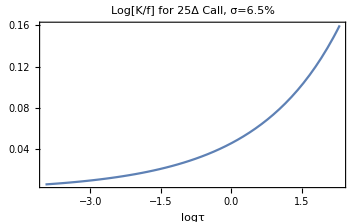

```mathematica
Plot[Log[Kfromσδf[1,0.065,0.25,ⅇ^logτ]],{logτ,Log[7/365],Log[10]},PlotRange->All,PlotLabel->"Log[K/f] for 25Δ Call, σ=6.5%",ImageSize->Medium,Frame->True,FrameLabel->"logτ"]
```

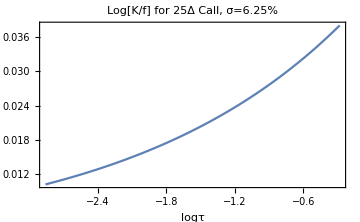

```mathematica
Plot[Log[Kfromσδf[1,0.0625,0.25,ⅇ^logτ]],{logτ,Log[21/365],Log[275/365]},PlotRange->All,PlotLabel->"Log[K/f] for 25Δ Call, σ=6.25%",ImageSize->Medium,Frame->True,FrameLabel->"logτ"]
```

```mathematica
mktstrikesf[atmf_,rr25_,st25_,rr10_,st10_,f_,τ_]:=
Module[{kcstr25d,kpstr25d,kcstr10d,kpstr10d,kcrr25d,kprr25d,kcrr10d,kprr10d},
kcstr25d=Kfromσδf[f,atmf+st25,+0.25,τ];
kpstr25d=Kfromσδf[f,atmf+st25,-0.25,τ];
kcstr10d=Kfromσδf[f,atmf+st10,+0.10,τ];
kpstr10d=Kfromσδf[f,atmf+st10,-0.10,τ];
kcrr25d=Kfromσδf[f,atmf+rr25/2+st25,+0.25,τ];
kprr25d=Kfromσδf[f,atmf-rr25/2+st25,-0.25,τ];
kcrr10d=Kfromσδf[f,atmf+rr10/2+st10,+0.10,τ];
kprr10d=Kfromσδf[f,atmf-rr10/2+st10,-0.10,τ];
{{f,f},{kcrr25d,kprr25d},{kcstr25d,kpstr25d},{kcrr10d,kprr10d},{kcstr10d,kpstr10d}}];
mktstrikesf::"usage"="mktstrikesf[atmf,rr25,st25,rr10,st10,f,τ] returns the strikes for the traded structures {atmf straddle,rr25d,str25d,rr10d,str10d}";

mktstrikesd[atm_,rr25_,st25_,rr10_,st10_,f_,τ_]:=
Module[{kcstr25d,kpstr25d,kcstr10d,kpstr10d,kcrr25d,kprr25d,kcrr10d,kprr10d},
kcstr25d=Kfromσδf[f,atm+st25,+0.25,τ];
kpstr25d=Kfromσδf[f,atm+st25,-0.25,τ];
kcstr10d=Kfromσδf[f,atm+st10,+0.10,τ];
kpstr10d=Kfromσδf[f,atm+st10,-0.10,τ];
kcrr25d=Kfromσδf[f,atm+rr25/2+st25,+0.25,τ];
kprr25d=Kfromσδf[f,atm-rr25/2+st25,-0.25,τ];
kcrr10d=Kfromσδf[f,atm+rr10/2+st10,+0.10,τ];
kprr10d=Kfromσδf[f,atm-rr10/2+st10,-0.10,τ];
{{f ⅇ^((atm^2 τ)/2),f ⅇ^((atm^2 τ)/2)},{kcrr25d,kprr25d},{kcstr25d,kpstr25d},{kcrr10d,kprr10d},{kcstr10d,kpstr10d}}];
mktstrikesf::"usage"="mktstrikesf[atm,rr25,st25,rr10,st10,f,τ] returns the strikes for the traded structures {atm straddle,rr25d,str25d,rr10d,str10d}";

smlmktstrikesf[atm_,rr25_,st25_,rr10_,st10_,f_,τ_]:=
Module[{kcstr25d,kpstr25d,kcstr10d,kpstr10d},
kcstr25d=Kfromσδf[f,atm+st25,+0.25,τ];
kpstr25d=Kfromσδf[f,atm+st25,-0.25,τ];
kcstr10d=Kfromσδf[f,atm+st10,+0.10,τ];
kpstr10d=Kfromσδf[f,atm+st10,-0.10,τ];
{{f,f},{kcstr25d,kpstr25d},{kcstr10d,kpstr10d}}];
smlmktstrikesf::"usage"="smlmktstrikesf[atm,rr25,st25,rr10,st10,f,τ] returns the strikes for the traded structures {atm straddle,str25d,str10d} (inverted quote)";
```

```mathematica
combpremiumf[ls_,{k1_,k2_},{σ1_,σ2_},f_,τ_]:=bspremium[1,f,k1,0,0,σ1,τ]+ls bspremium[-1,f,k2,0,0,σ2,τ];
combpremiumf::"usage"="combpremiumf[ls,{k1,k2},{σ1,σ2},f,τ] returns the premium for a traded structure {atm straddle,rr25d,str25d,rr10d,str10d} (inverted quote)";
stratpremiaf[strats_,strikes_,vols_,f_,τ_]:=MapThread[combpremiumf[#1,#2,#3,f,τ]&,{strats,strikes,vols}];
stratpremiaf::"usage"="stratpremiaf[strats,strikes,vols,f,τ] returns the premia for the traded structures {atm straddle,rr25d,str25d,rr10d,str10d} (inverted quote)";
```

```mathematica
volsfromparam5[0.05877, 0.00148, 0.00144,0.00257,0.00430]
```

{0.061785,0.05947,0.05877,0.06095,0.064355}

```mathematica
volsfrommkt[0.05877, 0.00148, 0.00144,0.00257,0.00430]
```

{{0.05877,0.05877},{0.06095,0.05947},{0.06021,0.06021},{0.064355,0.061785},{0.06307,0.06307}}

```mathematica
mktstrikesd[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365]
```

{{1.22248,1.22248},{1.23723,1.20828},{1.23704,1.2081},{1.25225,1.19461},{1.25165,1.19405}}

```mathematica
stratpremiaf[{1,-1,1,-1,1},
mktstrikesd[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365],
volsfrommkt[0.05877, 0.00148, 0.00144,0.00257,0.00430],1.2223,31/365]
```

{0.0167052,0.0000224137,0.00639846,0.0000271008,0.00212738}

```mathematica
stratpremiaf[{1,-1,1,-1,1},
mktstrikesd[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365],
volsfrommkt[0.05877, 0.00148, 0.00144,0.00257,0.00430],1.2223,31/365]*10^6
```

{16705.2,22.4137,6398.46,27.1008,2127.38}

```mathematica
volsfrommkt[0.216215, -0.005, 0.007375,0,0]
```

{{0.216215,0.216215},{0.22109,0.22609},{0.22359,0.22359},{0.216215,0.216215},{0.216215,0.216215}}

```mathematica
mktstrikesd[0.216215, -0.005, 0.007375,0,0,1.3070,0.0849]
```

{{1.3096,1.3096},{1.36788,1.25291},{1.36861,1.25347},{1.41972,1.20802},{1.41972,1.20802}}

```mathematica
Kλ[u_,λ_]:=ⅇ^(-1/2(u/λ)^2);
```

```mathematica
Nxs[x_,xs_]:=Map[Abs[x-#]&,xs];
```

```mathematica
Ksλ[x_,λ_,xs_,nk_]:=Map[Kλ[#,λ]&,Nxs[x,xs]];
```

```mathematica
Φλ[x_,λ_,xs_,nk_]:=Total[Map[Kλ[#,λ]&,Nxs[x,xs]]];
```

```mathematica
g[x_,λ_,αs_,xs_,nk_]:=Dot[αs,Ksλ[x,λ,xs,nk]]/Φλ[x,λ,xs,nk];
```

```mathematica
extrapolate[anchors_,vols_]:=Module[{dac,dap,dvc,dvp},
dac=2anchors[[4]]-anchors[[2]];
dap=2anchors[[5]]-anchors[[3]];
dvc=2vols[[4]]-vols[[2]];
dvp=2vols[[5]]-vols[[3]];
{Join[anchors,{dac,dap}],Join[vols,{dvc,dvp}]}];
```

```mathematica
extrapolateslope[anchors_,vols_]:=Module[{dac,dap,dvc,dvp},
dac=anchors[[4]]-anchors[[2]];
dap=anchors[[5]]-anchors[[3]];
dvc=vols[[4]]-vols[[2]];
dvp=vols[[5]]-vols[[3]];
{dvc/dac,dvp/dap}];
```

```mathematica
gtail[x_,λ_,αs_,xs_,nk_,sc_,sp_]:=Module[{xp,σp,xc,σc},
xp=Min[xs];σp=g[xp,λ,αs,xs,nk];
xc=Max[xs];σc=g[xc,λ,αs,xs,nk];
Piecewise[{{σc+( x-xc)sc, x>xc}, {σp+ (x-xp)sp, x< xp}, {g[x,λ,αs,xs,nk], True}}]];
```

```mathematica
interpolvol[atm_,rr25_,st25_,rr10_,st10_,f_,τ_]:=Module[
{volspairs,strikespairs,stratssigns,stratsleg1,stratsleg2,stratslegs,
premiapairs,logks,λ,
npts,anchors,vols,sol,αsol,
(*npts7,anchors7,vols7,sol7,αsol7,*)
(*args,diffs,*)
eqatm,eqrr25,eqrr10,eqst25,eqst10,
soleq,αsoleq,soleqvols,
sp,sc,
deltas,λδ,solδ,αsolδ},

volspairs=volsfrommkt[atm,rr25,st25,rr10,st10];
strikespairs=mktstrikesd[atm,rr25,st25,rr10,st10,f,τ];
(*stratssigns=Transpose[{{1,1,1,1,1},{-1,-1,-1,-1,-1}}];
stratsleg1={1,1,1,1,1};
stratsleg2={1,-1,1,-1,1};
premiapairs=stratpremiaf[stratsleg2,strikespairs,volspairs,f,τ];
stratslegs=Transpose[{stratsleg1,stratsleg2}];*)
logks=Log[strikespairs/f];
npts=5;
anchors={logks⟦1,1⟧,logks⟦2,1⟧,logks⟦2,2⟧,logks⟦4,1⟧,logks⟦4,2⟧};
vols={volspairs⟦1,1⟧,volspairs⟦2,1⟧,volspairs⟦2,2⟧,volspairs⟦4,1⟧,volspairs⟦4,2⟧};
λ=(logks⟦2,1⟧-logks⟦2,2⟧)/2;

sol=First[Solve[MapThread[g[#1,λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts]==#2&,{anchors,vols}],
Table[Subscript[α, j],{j,1,npts}]]];
αsol=Map[Last,sol];

eqatm=g[(atm^2 τ)/2,λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts]-atm;
eqrr25=g[anchors[[2]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts]-
g[anchors[[3]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts]-rr25;
eqrr10=g[anchors[[4]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts]-
g[anchors[[5]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts]-rr10;
eqst25=(bspremium[1,f,strikespairs[[3,1]],0,0,g[logks[[3,1]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts],τ]+
bspremium[-1,f,strikespairs[[3,2]],0,0,g[logks[[3,2]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts],τ])-(
bspremium[1,f,strikespairs[[3,1]],0,0,volspairs[[3,1]],τ]+
bspremium[-1,f,strikespairs[[3,2]],0,0,volspairs[[3,2]],τ]);
eqst10=(bspremium[1,f,strikespairs[[5,1]],0,0,g[logks[[5,1]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts],τ]+
bspremium[-1,f,strikespairs[[5,2]],0,0,g[logks[[5,2]],λ,Table[Subscript[α, j],{j,1,npts}],anchors,npts],τ])-(
bspremium[1,f,strikespairs[[5,1]],0,0,volspairs[[5,1]],τ]+
bspremium[-1,f,strikespairs[[5,2]],0,0,volspairs[[5,2]],τ]);
soleq=FindRoot[{eqatm,eqrr25,eqrr10,eqst25,eqst10},Transpose[{Table[Subscript[α, j],{j,1,npts}],αsol}]];
αsoleq=Map[Last,soleq];

soleqvols=Map[g[#,λ,αsoleq,anchors,npts]&,anchors];
{sc,sp}=extrapolateslope[anchors,soleqvols];

(* diffs=MapThread[{Dot[#1,#2],#3}&,{stratslegs,Map[Apply[bspremium,#]&,args/.sol2,{2}],premiapairs}]; *)
deltas={0.50,0.25,0.75,0.10,0.90};
λδ=0.25;
solδ=First[Solve[MapThread[g[#1,λδ,Table[Subscript[α, j],{j,1,npts}],deltas,npts]==#2&,{deltas,vols}]]];
αsolδ=Map[Last,solδ];
{anchors,vols,deltas,{λ,λδ},αsoleq,soleqvols,αsolδ,{sc,sp}}
];
```

```mathematica
Grid[interpolvol[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365]]
```

0.000146673 | 0.0121385 | -0.0115396 | 0.0242114 | -0.0229135
0.05877 | 0.06095 | 0.05947 | 0.064355 | 0.061785
0.5 | 0.25 | 0.75 | 0.1 | 0.9
0.0118391 | 0.25 |  |  | 
0.0576963 | 0.0589605 | 0.0566463 | 0.068479 | 0.0656629
0.05877 | 0.0609566 | 0.0594766 | 0.0643508 | 0.0617808
0.0788643 | 0.0272054 | 0.0299293 | 0.0924017 | 0.0846388
0.281148 | -0.202592 |  |  |

```mathematica
interpolvol[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365]
```

{{0.000146673,0.0121385,-0.0115396,0.0242114,-0.0229135},{0.05877,0.06095,0.05947,0.064355,0.061785},{0.5,0.25,0.75,0.1,0.9},{0.0118391,0.25},{0.0576963,0.0589605,0.0566463,0.068479,0.0656629},{0.05877,0.0609566,0.0594766,0.0643508,0.0617808},{0.0788643,0.0272054,0.0299293,0.0924017,0.0846388},{0.281148,-0.202592}}

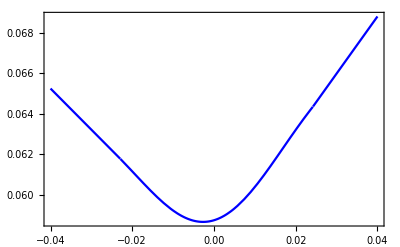

```mathematica
Plot[{
gtail[x,0.011839060322642678,{0.05769632193039086,0.05896050785540159,0.05664627516711007,0.06847902756025366,0.06566292829571305},{0.00014667301356155048,0.01213849159743891,-0.011539629047846446,0.02421135445649408,-0.022913520990713924},5,0.28114805595095743,-0.20259221154557136]},{x,-0.04,+0.04},PlotStyle->{Blue},Frame->True,PlotRange->All]
```

```mathematica
showplots[atm_,rr25_,st25_,rr10_,st10_,f_,τ_,title_,ζ_:3,size_:300]:=Module[{npts,anchors,vols,deltas,λ,λδ,αsoleq,soleqvols,αsolδ,sc,sp,xmin,xmax},
npts=5;
{anchors,vols,deltas,{λ,λδ},αsoleq,soleqvols,αsolδ,{sc,sp}}=interpolvol[atm,rr25,st25,rr10,st10,f,τ];
Print[Grid[{anchors,αsoleq,soleqvols,αsolδ,{sc,sp}}]];
xmin=ζ Min[anchors];xmax=ζ Max[anchors];
Grid[{{
(*First Chart*)
Show[
(*Plot σ(logK) with logstrike interpolation and extrapolation*)
Plot[gtail[x,λ,αsoleq,anchors,npts,sc,sp],{x,xmin,xmax},Frame->True,PlotStyle->{Darker[Green]},ImageSize->size,FrameLabel->{"Log[K/f]","σ"},PlotLabel->StringJoin[title," , LogStrike, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(logK) with logstrike interpolation*)
Plot[g[x,λ,αsoleq,anchors,npts],{x,xmin,xmax},Frame->True,PlotStyle->{Blue},ImageSize->size,FrameLabel->{"Log[K/f]","σ"},PlotLabel->StringJoin[title," , LogStrike, λ=",ToString[Round[λ,0.001]]]],
(*Plot points*)
ListPlot[Transpose[{anchors,vols}],Frame->True,PlotStyle->{PointSize[0.02],Red},PlotRange->All]
],
(*Second Chart*)
Show[
(*Plot σ(Δ) with logstrike interpolation and extrapolation*)
ParametricPlot[{bsdelta[1,f,f Exp[x],0,0,gtail[x,λ,αsoleq,anchors,npts,sc,sp],τ],gtail[x,λ,αsoleq,anchors,npts,sc,sp]},
{x,xmin,xmax},Frame->True,PlotStyle->{Darker[Green]},AspectRatio->2/3,AxesOrigin->{0.5,atm},ImageSize->size,FrameLabel->{"Δ_c","σ"},PlotLabel->StringJoin[title," , Delta, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(Δ) with logstrike interpolation*)
ParametricPlot[{bsdelta[1,f,f Exp[x],0,0,g[x,λ,αsoleq,anchors,npts],τ],g[x,λ,αsoleq,anchors,npts]},
{x,xmin,xmax},Frame->True,PlotStyle->{Blue},AspectRatio->2/3,AxesOrigin->{0.5,atm},ImageSize->size,FrameLabel->{"Δ_c","σ"},PlotLabel->StringJoin[title," , Delta, λ=",ToString[Round[λ,0.001]]]],
(*Plot points*)
ListPlot[Transpose[{{0.50,0.25,0.75,0.10,0.90},vols}],Frame->True,PlotStyle->{PointSize[0.02],Red}],
(*Plot σ(Δ) with Δ interpolation and extrapolation*)
Plot[g[x,λδ,αsolδ,deltas,npts],{x,0,1},Frame->True,PlotStyle->Gray,PlotRange->All]
],
(*Third Chart*)
Show[
(*Plot Premium(logk) puts from logstrike interpolation*)
Plot[bspremium[Sign[x],f,f Exp[x],0,0,g[x,λ,αsoleq,anchors,npts],τ],
{x,xmin,Min[anchors]},Frame->True,PlotStyle->{Blue},AspectRatio->3/4,AxesOrigin->{0,0},ImageSize->size,FrameLabel->{"Log[K/f]","Premium"},PlotRange->All,PlotLabel->StringJoin[title," , Premium, λ=",ToString[Round[λ,0.001]]]],
(*Plot Premium(logk) calls from logstrike interpolation*)
Plot[bspremium[Sign[x],f,f Exp[x],0,0,g[x,λ,αsoleq,anchors,npts],τ],
{x,Max[anchors],xmax},Frame->True,PlotStyle->{Blue},AspectRatio->3/4,AxesOrigin->{0,0},ImageSize->size,FrameLabel->{"Log[K/f]","Premium"},PlotRange->All,PlotLabel->StringJoin[title," , Premium, λ=",ToString[Round[λ,0.001]]]],
(*Plot Premium(logk) puts from logstrike interpolation and extrapolation*)
Plot[bspremium[Sign[x],f,f Exp[x],0,0,gtail[x,λ,αsoleq,anchors,npts,sc,sp],τ],
{x,xmin,Min[anchors]},Frame->True,PlotStyle->{Darker[Green]},AspectRatio->3/4,AxesOrigin->{0,0},ImageSize->size,FrameLabel->{"Log[K/f]","Premium"},PlotRange->All,PlotLabel->StringJoin[title," , Premium, λ=",ToString[Round[λ,0.001]]]],
(*Plot Premium(logk) calls from logstrike interpolation and extrapolation*)
Plot[bspremium[Sign[x],f,f Exp[x],0,0,gtail[x,λ,αsoleq,anchors,npts,sc,sp],τ],
{x,Max[anchors],xmax},Frame->True,PlotStyle->{Darker[Green]},AspectRatio->3/4,AxesOrigin->{0,0},ImageSize->size,FrameLabel->{"Log[K/f]","Premium"},PlotRange->All,PlotLabel->StringJoin[title," , Premium, λ=",ToString[Round[λ,0.001]]]]
],
(*Fourth Chart*)
Show[
(*Plot σ(Δ) puts from logstrike interpolation and extrapolation*)
ParametricPlot[{-bsdelta[Sign[x],f,f Exp[x],0,0,gtail[x,λ,αsoleq,anchors,npts,sc,sp],τ],gtail[x,λ,αsoleq,anchors,npts,sc,sp]},
{x,xmin,Min[anchors]},Frame->True,PlotStyle->{Darker[Green]},AspectRatio->3/4,AxesOrigin->{0,atm+rr10/2+st10},ImageSize->size,FrameLabel->{"Δ","σ"},PlotRange->All,PlotLabel->StringJoin[title," , Tail, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(Δ) calls from logstrike interpolation and extrapolation*)
ParametricPlot[{bsdelta[Sign[x],f,f Exp[x],0,0,gtail[x,λ,αsoleq,anchors,npts,sc,sp],τ],gtail[x,λ,αsoleq,anchors,npts,sc,sp]},
{x,Max[anchors],xmax},Frame->True,PlotStyle->{Dashed,Darker[Green]},AspectRatio->3/4,AxesOrigin->{0,atm+rr10/2+st10},ImageSize->size,FrameLabel->{"Δ","σ"},PlotRange->All,PlotLabel->StringJoin[title," , Tail, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(Δ) puts from logstrike interpolation*)
ParametricPlot[{-bsdelta[Sign[x],f,f Exp[x],0,0,g[x,λ,αsoleq,anchors,npts],τ],g[x,λ,αsoleq,anchors,npts]},
{x,xmin,Min[anchors]},Frame->True,PlotStyle->{Blue},AspectRatio->3/4,AxesOrigin->{0,atm+rr10/2+st10},ImageSize->size,FrameLabel->{"Δ","σ"},PlotRange->All,PlotLabel->StringJoin[title," , Tail, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(Δ) calls from logstrike interpolation*)
ParametricPlot[{bsdelta[Sign[x],f,f Exp[x],0,0,g[x,λ,αsoleq,anchors,npts],τ],g[x,λ,αsoleq,anchors,npts]},
{x,Max[anchors],xmax},Frame->True,PlotStyle->{Dashed,Blue},AspectRatio->3/4,AxesOrigin->{0,atm+rr10/2+st10},ImageSize->size,FrameLabel->{"Δ","σ"},PlotRange->All,PlotLabel->StringJoin[title," , Tail, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(Δ) puts from Δ interpolation*)
ParametricPlot[{1-x,g[x,λδ,αsolδ,deltas,npts]},
{x,0.875,1},Frame->True,PlotStyle->{Gray},AspectRatio->3/4,AxesOrigin->{0,atm+rr10/2+st10},ImageSize->size,FrameLabel->{"Δ","σ"},PlotRange->All,PlotLabel->StringJoin[title," , Tail, λ=",ToString[Round[λ,0.001]]]],
(*Plot σ(Δ) calls from Δ interpolation*)
ParametricPlot[{x,g[x,λδ,αsolδ,deltas,npts]},
{x,0,0.125},Frame->True,PlotStyle->{Dashed,Gray},AspectRatio->3/4,AxesOrigin->{0,atm+rr10/2+st10},ImageSize->size,FrameLabel->{"Δ","σ"},PlotRange->All,PlotLabel->StringJoin[title," , Tail, λ=",ToString[Round[λ,0.001]]]]]
}}]]
```

#### FX Smile interpolation - SVI

```mathematica
varSVI[k_,a_,b_,σ_,ρ_,m_]:=a+b(ρ(k-m)+Sqrt[(k-m)^2+σ^2]);
varSVI::"usage"="varSVI[k,a,b,σ,ρ,m] returns the SVI variance given the parameters a,b,σ,ρ,m and the logstrike k = Log[K/F]";
volSVI[k_,a_,b_,σ_,ρ_,m_]:=Sqrt[a+b(ρ(k-m)+Sqrt[(k-m)^2+σ^2])];
volSVI::"usage"="volSVI[k,a,b,σ,ρ,m] returns the SVI volatility given the parameters a,b,σ,ρ,m and the logstrike k = Log[K/F]";
```

```mathematica
interpolvol[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365]
```

{{0.000146673,0.0121385,-0.0115396,0.0242114,-0.0229135},{0.05877,0.06095,0.05947,0.064355,0.061785},{0.5,0.25,0.75,0.1,0.9},{0.0118391,0.25},{0.0576963,0.0589605,0.0566463,0.068479,0.0656629},{0.05877,0.0609566,0.0594766,0.0643508,0.0617808},{0.0788643,0.0272054,0.0299293,0.0924017,0.0846388},{0.281148,-0.202592}}

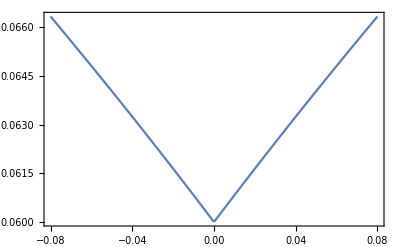

```mathematica
Plot[volSVI[k,0.06^2,0.01,0,0,0],{k,-0.08,+0.08},Frame->True,PlotRange->All]
```

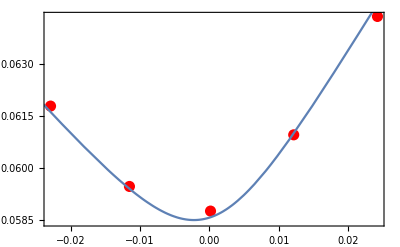

```mathematica
Show[ListPlot[Transpose[{{0.00014667301356155048,0.01213849159743891,-0.011539629047846446,0.02421135445649408,-0.022913520990713924},{0.058770000000000024,0.06095655405998937,0.05947655405998937,0.06435081598257525,0.061780815982575246}}],PlotRange->All,PlotStyle->{PointSize[0.02],Red},Frame->True]
,Plot[volSVI[k,(0.055)^2,0.037,0.011,0.2,0],{k,-0.08,+0.08},Frame->True,PlotRange->All]]
```

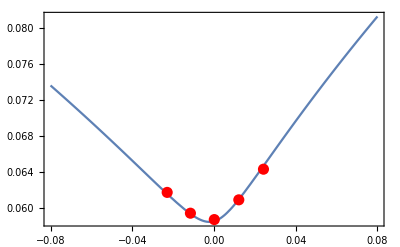

```mathematica
Show[Plot[volSVI[k,(0.055)^2,0.037,0.011,0.2,0],{k,-0.08,+0.08},Frame->True,PlotRange->All],ListPlot[Transpose[{{0.00014667301356155048,0.01213849159743891,-0.011539629047846446,0.02421135445649408,-0.022913520990713924},{0.058770000000000024,0.06095655405998937,0.05947655405998937,0.06435081598257525,0.061780815982575246}}],PlotRange->All,PlotStyle->{PointSize[0.02],Red},Frame->True]
]
```

0.000146673 | 0.0121385 | -0.0115396 | 0.0242114 | -0.0229135
0.0576963 | 0.0589605 | 0.0566463 | 0.068479 | 0.0656629
0.05877 | 0.0609566 | 0.0594766 | 0.0643508 | 0.0617808
0.0788643 | 0.0272054 | 0.0299293 | 0.0924017 | 0.0846388
0.281148 | -0.202592 |  |  |

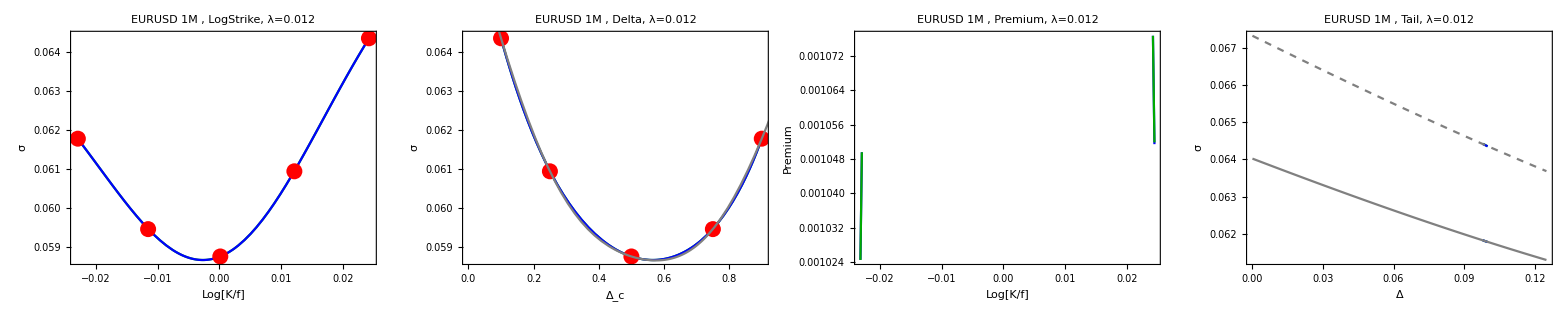

```mathematica
showplots[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365,"EURUSD 1M",1.01,Large]
```

0.000146673 | 0.0121385 | -0.0115396 | 0.0242114 | -0.0229135
0.0576963 | 0.0589605 | 0.0566463 | 0.068479 | 0.0656629
0.05877 | 0.0609566 | 0.0594766 | 0.0643508 | 0.0617808
0.0788643 | 0.0272054 | 0.0299293 | 0.0924017 | 0.0846388
0.281148 | -0.202592 |  |  |

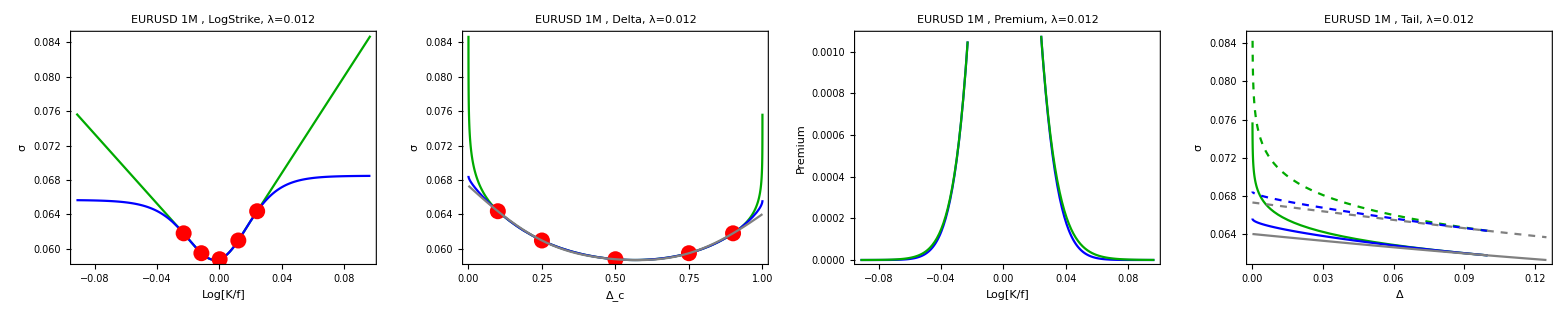

```mathematica
showplots[0.05877, 0.00148, 0.00144,0.00257,0.00430,1.2223,31/365,"EURUSD 1M",4,Large]
```

0.000429677 | 0.0211253 | -0.0197346 | 0.0428123 | -0.040188
0.0575259 | 0.0580126 | 0.0554005 | 0.0711073 | 0.0688409
0.05839 | 0.0610067 | 0.0596067 | 0.0656922 | 0.0632422
0.0910503 | 0.00941381 | 0.0121405 | 0.107275 | 0.0997698
0.216049 | -0.177744 |  |  |

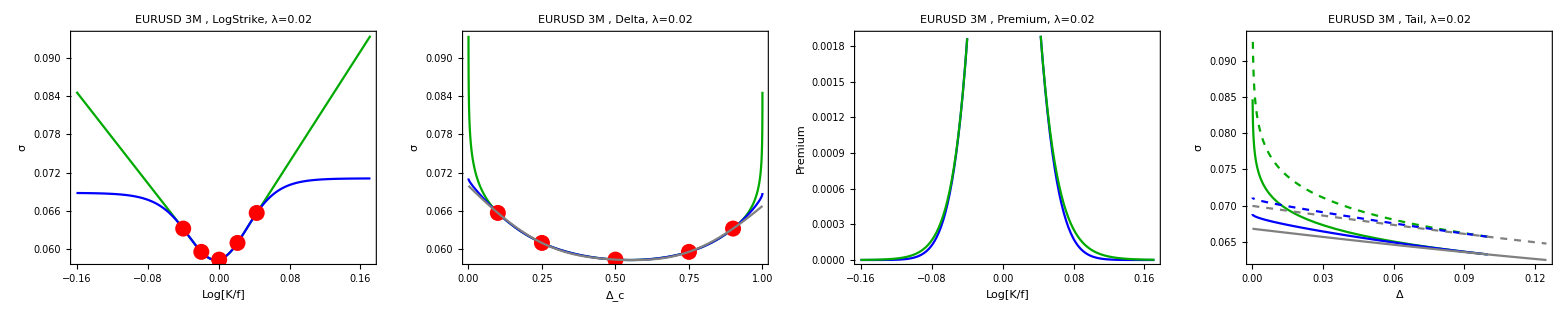

```mathematica
showplots[0.05839, 0.00140, 0.00191,0.00245,0.00608,1.2238,92/365,"EURUSD 3M",4,Large]
```

0.000913457 | 0.03138 | -0.0288164 | 0.0646169 | -0.0603318
0.0580024 | 0.0604607 | 0.0578531 | 0.0760113 | 0.0744593
0.0602 | 0.0634162 | 0.0622162 | 0.0696694 | 0.0675694
0.106613 | -0.00827217 | -0.00593499 | 0.126773 | 0.12034
0.188141 | -0.16986 |  |  |

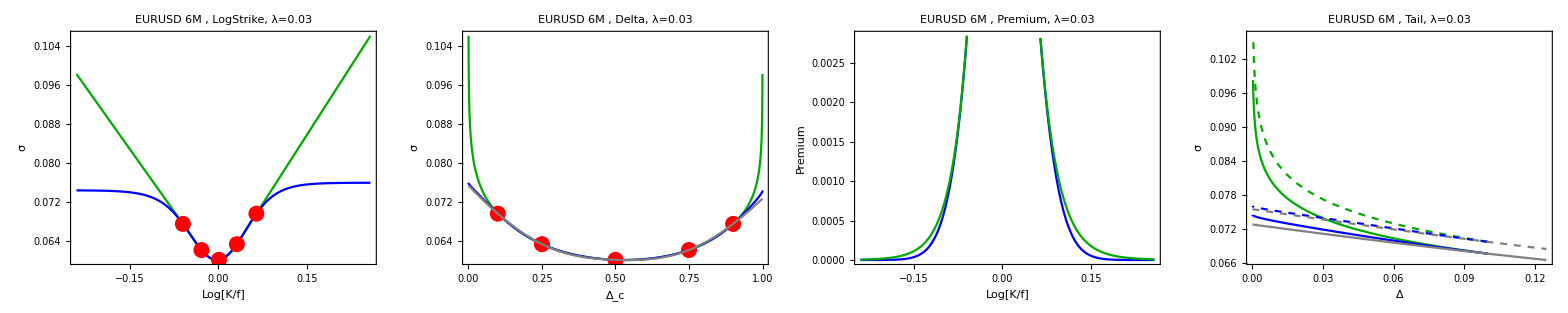

```mathematica
showplots[0.06020, 0.00120, 0.00261,0.00210,0.00842,1.2260,184/365,"EURUSD 6M",4,Large]
```

0.00207304 | 0.047224 | -0.0440775 | 0.0979456 | -0.0973101
0.0620927 | 0.0609942 | 0.0648215 | 0.0828053 | 0.0867513
0.06439 | 0.0667157 | 0.0688657 | 0.0742449 | 0.0782949
0.139871 | -0.0389341 | -0.0454017 | 0.154111 | 0.168098
0.148441 | -0.177132 |  |  |

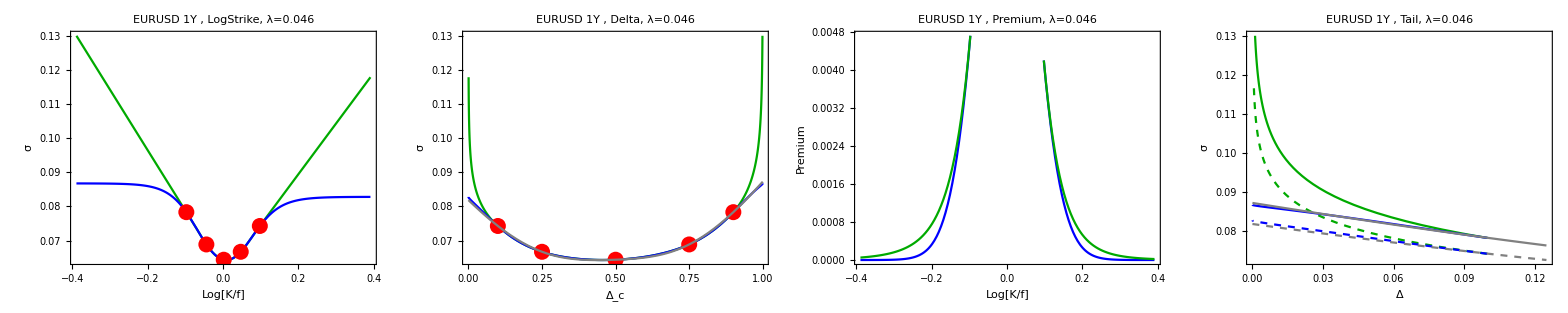

```mathematica
showplots[0.06439, -0.00215, 0.00340,-0.00405,0.01191,1.2308,365/365,"EURUSD 1Y",4,Large]
```

C[K_2]=((K_2-S_0)/(K_1-S_0))^(1-α)C[K_1]

```mathematica
With[{α=2.5,S0=1,δ=0.1,σ1=0.145,τ=1/4},K1=S0(1+δ);bsdelta[1,S0,K1,0,0,σ1,τ]]
```

0.100559

```mathematica
With[{α=3.5,S0=1,δ=0.1,σ1=0.145,τ=1/4},
K1=S0(1+δ);
Plot3D[{((K2-S0)/(K1-S0))^(1-α)},{K2,K1,K1(1+δ)^2},{σ2,σ1,3σ1},PlotRange->All,AxesLabel->Automatic,ColorFunction->(ColorData["TemperatureMap"][#3]&)]]
```

-Graphics3D-

```mathematica
σK[K1_,K2_,σ1_,δσ_]:=σ1+Log[K2/K1]δσ;
```

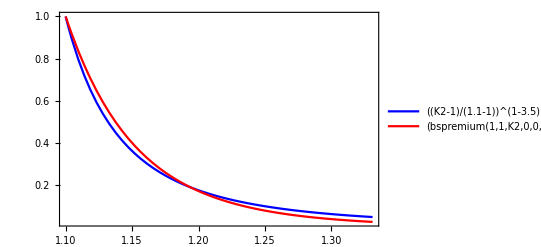

```mathematica
With[{α=3.5,S0=1,δ=0.1,K1=1(1+0.1),σ1=0.145,τ=1/4,δσ=1/3.2},
Plot[{((K2-S0)/(K1-S0))^(1-α),(bspremium[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]/bspremium[1,S0,K1,0,0,σ1,τ])},{K2,K1,K1(1+δ)^2},
PlotRange->All,Frame->True,PlotLegends->"Expressions",PlotStyle->{Blue,Red}]]
```

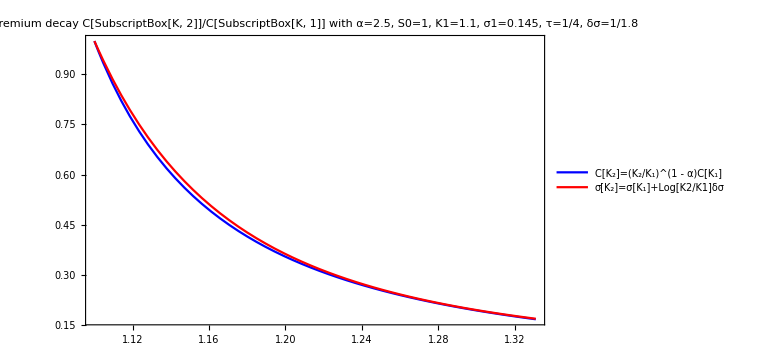

```mathematica
With[{α=2.5,S0=1,δ=0.1,K1=1(1+0.1),σ1=0.145,τ=1/4,δσ=1/1.8},
Plot[{((K2-S0)/(K1-S0))^(1-α),(bspremium[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]/bspremium[1,S0,K1,0,0,σ1,τ])},{K2,K1,K1(1+δ)^2},
PlotRange->All,Frame->True,PlotLegends->{"C[K_2]=(K_2/K_1)^(1 - α)C[K_1]","σ[K_2]=σ[K_1]+Log[K2/K1]δσ"},
PlotStyle->{Blue,Red},ImageSize->Large,PlotLabel->"Premium decay C[SubscriptBox[K, 2]]/C[SubscriptBox[K, 1]] with α=2.5, S0=1, K1=1.1, σ1=0.145, τ=1/4, δσ=1/1.8"]]
```

```mathematica
Refine[bsdelta[1,f,K,0,0,σ,τ],τ>0&&f≠K]
```

1/2 Erfc[-((σ^2 τ)/2+Log[f/K])/(√2 σ √τ)]

((σ^2 τ)/2+Log[f/K])/(√2 σ √τ)==-InverseErfc[2δ]

((σ √τ)^2/2+Log[f/K])/(σ √τ)==-√2InverseErfc[2δ]

1/2 σ √τ+Log[f/K]/(σ √τ)==-√2InverseErfc[2δ]

Log[f/K]/(σ √τ)==-√2InverseErfc[2δ]-1/2 σ √τ

Log[f/K]==-σ √τ(√2 InverseErfc[2δ]+1/2 σ √τ)

Log[K/f]==σ √τ(√2 InverseErfc[2δ]+1/2 σ √τ)

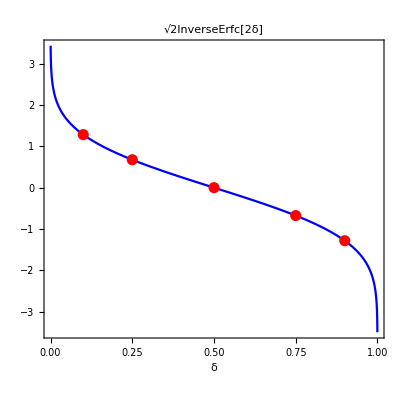

```mathematica
Show[Plot[√2 InverseErfc[2δ],{δ,0,1},AspectRatio->1,Frame->True,PlotStyle->Blue,AxesOrigin->{1/2,0},FrameLabel->{"δ"},PlotLabel->"√2InverseErfc[2δ]"],
ListPlot[Map[{#,√2 InverseErfc[2#]}&,{0.50,0.25,0.75,0.10,0.90}],AspectRatio->1,Frame->True,PlotStyle->{PointSize[0.02],Red},AxesOrigin->{1/2,0}]]
```

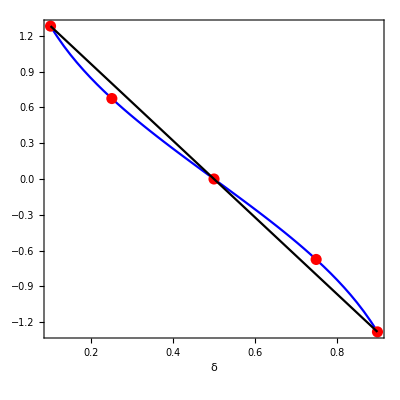

```mathematica
Show[Plot[√2 InverseErfc[2δ],{δ,0.1,1-0.1},AspectRatio->1,Frame->True,PlotStyle->Blue,AxesOrigin->{1/2,0},FrameLabel->{"δ"}],
ListPlot[Map[{#,√2 InverseErfc[2#]}&,{0.50,0.25,0.75,0.10,0.90}],AspectRatio->1,Frame->True,PlotStyle->{PointSize[0.02],Red},AxesOrigin->{1/2,0}],
ListLinePlot[Map[{#,√2 InverseErfc[2#]}&,{0.10,0.90}],AspectRatio->1,Frame->True,PlotStyle->{Black},AxesOrigin->{1/2,0}]]
```

```mathematica
σMalz[atm_,rr25_,st25_,δ_]:=atm-2rr25(δ-1/2)+16st25(δ-1/2)^2;
```

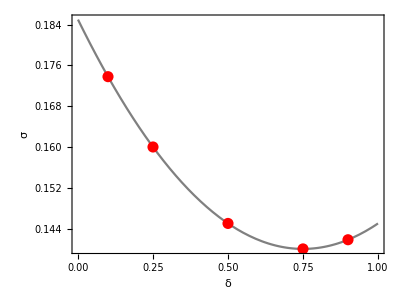

```mathematica
With[{atm=0.145,rr25=0.02,st25=0.005},Show[Plot[σMalz[atm,rr25,st25,δ],{δ,0,1},AspectRatio->3/4,Frame->True,PlotStyle->Gray,AxesOrigin->{1/2,atm},FrameLabel->{"δ","σ"}],
ListPlot[Map[{#,σMalz[atm,rr25,st25,#]}&,{0.50,0.25,0.75,0.10,0.90}],AspectRatio->3/4,Frame->True,PlotStyle->{PointSize[0.02],Red},AxesOrigin->{1/2,atm}]]]
```

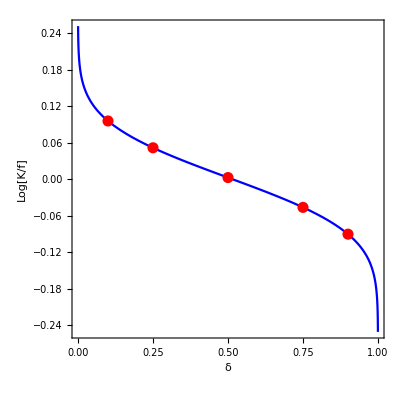

```mathematica
With[{σ=0.145,τ=1/4},Show[Plot[σ √τ(√2 InverseErfc[2δ]+1/2 σ √τ),{δ,0,1},AspectRatio->1,Frame->True,PlotStyle->Blue,AxesOrigin->{1/2,0},FrameLabel->{"δ","Log[K/f]"}],
ListPlot[Map[{#,σ √τ(√2 InverseErfc[2#]+1/2 σ √τ)}&,{0.50,0.25,0.75,0.10,0.90}],AspectRatio->1,Frame->True,PlotStyle->{PointSize[0.02],Red},AxesOrigin->{1/2,0}]]]
```

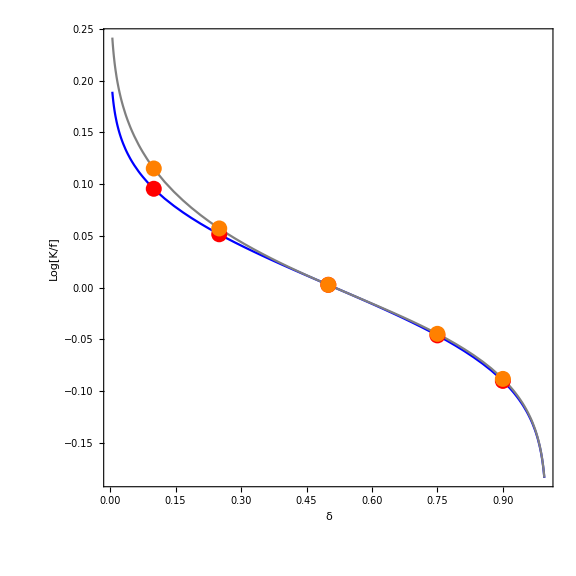

```mathematica
With[{σ=0.145,atm=0.145,rr25=0.02,st25=0.005,τ=1/4},Show[Plot[{
σ √τ(√2 InverseErfc[2δ]+1/2 σ √τ),
σMalz[atm,rr25,st25,δ] √τ(√2 InverseErfc[2δ]+1/2 σMalz[atm,rr25,st25,δ] √τ)},
{δ,0.005,1-0.005},AspectRatio->1,Frame->True,PlotStyle->{Blue,Gray},
AxesOrigin->{1/2,0},FrameLabel->{"δ","Log[K/f]"},PlotRange->All,ImageSize->Large],
ListPlot[{Map[{#,σ √τ(√2 InverseErfc[2#]+1/2 σ √τ)}&,{0.50,0.25,0.75,0.10,0.90}],
Map[{#,σMalz[atm,rr25,st25,#] √τ(√2 InverseErfc[2#]+1/2 σMalz[atm,rr25,st25,#] √τ)}&,{0.50,0.25,0.75,0.10,0.90}]},
AspectRatio->1,Frame->True,PlotStyle->{{PointSize[0.02],Red},{PointSize[0.02],Orange}},AxesOrigin->{1/2,0}]]]
```

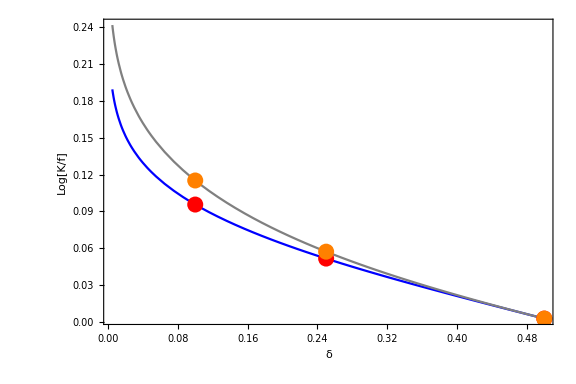

```mathematica
With[{σ=0.145,atm=0.145,rr25=0.02,st25=0.005,τ=1/4},Show[Plot[{
σ √τ(√2 InverseErfc[2δ]+1/2 σ √τ),
σMalz[atm,rr25,st25,δ] √τ(√2 InverseErfc[2δ]+1/2 σMalz[atm,rr25,st25,δ] √τ)},
{δ,0.005,0.5},AspectRatio->2/3,Frame->True,PlotStyle->{Blue,Gray},
AxesOrigin->{1/2,0},FrameLabel->{"δ","Log[K/f]"},PlotRange->All,ImageSize->Large],
ListPlot[{Map[{#,σ √τ(√2 InverseErfc[2#]+1/2 σ √τ)}&,{0.50,0.25,0.10}],
Map[{#,σMalz[atm,rr25,st25,#] √τ(√2 InverseErfc[2#]+1/2 σMalz[atm,rr25,st25,#] √τ)}&,{0.50,0.25,0.10}]},
AspectRatio->1,Frame->True,PlotStyle->{{PointSize[0.02],Red},{PointSize[0.02],Orange}},AxesOrigin->{1/2,0}]]]
```

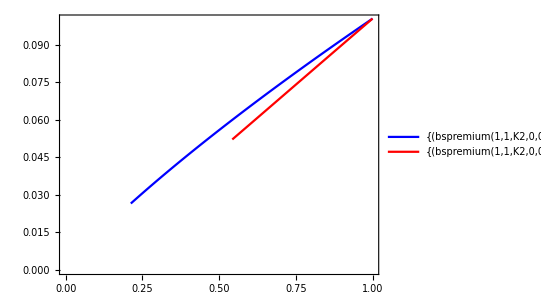

```mathematica
With[{α=2.5,S0=1,δ=0.1,K1=1(1+0.1),σ1=0.145,τ=1/4,δσ=1/1.8},
ParametricPlot[{{(bspremium[1,S0,K2,0,0,σ1,τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σ1,τ]},
{(bspremium[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]}},
{K2,K1,K1(1+δ)^0.5},
PlotRange->{{0,1},{0,0.10}},Frame->True,PlotLegends->"Expressions",PlotStyle->{Blue,Red},AspectRatio->3/4]]
```

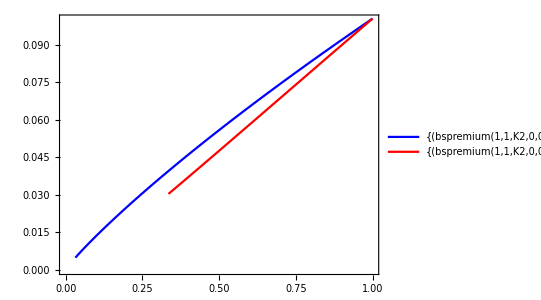

```mathematica
With[{α=2.5,S0=1,δ=0.1,K1=1(1+0.1),σ1=0.145,τ=1/4,δσ=1/1.8},
ParametricPlot[{{(bspremium[1,S0,K2,0,0,σ1,τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σ1,τ]},
{(bspremium[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]}},
{K2,K1,K1(1+δ)^1},
PlotRange->{{0,1},{0,0.10}},Frame->True,PlotLegends->"Expressions",PlotStyle->{Blue,Red},AspectRatio->3/4]]
```

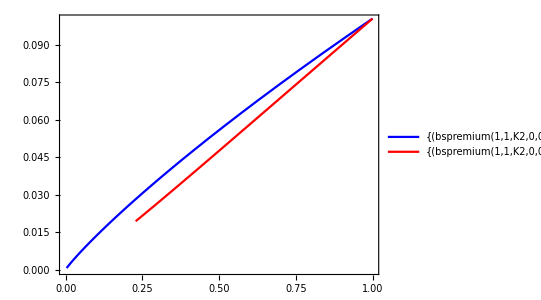

```mathematica
With[{α=2.5,S0=1,δ=0.1,K1=1(1+0.1),σ1=0.145,τ=1/4,δσ=1/1.8},
ParametricPlot[{{(bspremium[1,S0,K2,0,0,σ1,τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σ1,τ]},
{(bspremium[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]}},
{K2,K1,K1(1+δ)^1.5},
PlotRange->{{0,1},{0,0.10}},Frame->True,PlotLegends->"Expressions",PlotStyle->{Blue,Red},AspectRatio->3/4]]
```

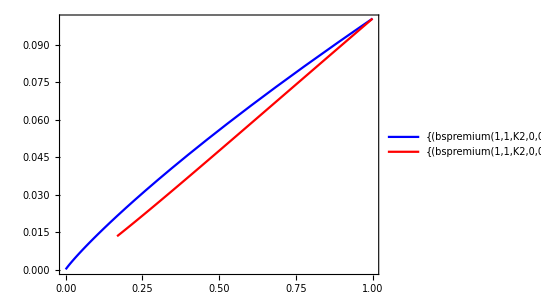

```mathematica
With[{α=2.5,S0=1,δ=0.1,K1=1(1+0.1),σ1=0.145,τ=1/4,δσ=1/1.8},
ParametricPlot[{{(bspremium[1,S0,K2,0,0,σ1,τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σ1,τ]},
{(bspremium[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]/bspremium[1,S0,K1,0,0,σ1,τ]),bsdelta[1,S0,K2,0,0,σK[K1,K2,σ1,δσ],τ]}},
{K2,K1,K1(1+δ)^2},
PlotRange->{{0,1},{0,0.10}},Frame->True,PlotLegends->"Expressions",PlotStyle->{Blue,Red},AspectRatio->3/4]]
```

### Monte Carlo - Paths

```mathematica
MCPath[steps_,S0_,drift_,vol_,t_]:=Module[{dt,ntable,logreturns,spath,drifta,vola},dt=t/steps;ntable=Table[Random[NormalDistribution[0,1]],{steps}];If[VectorQ[drift],drifta=drift,drifta=Table[drift,{steps}]];If[VectorQ[vol],vola=vol,vola=Table[vol,{steps}]];logreturns=Accumulate[Table[If[i==0,0,(drifta⟦i⟧-vola⟦i⟧^2/2) dt+vola⟦i⟧ √dt ntable⟦i⟧],{i,0,steps}]];spath=S0 ⅇ^logreturns;spath];
MCPath::"usage"="MCPath[steps,S0,drift,vol,t] returns a MC path";
MCPathPair[steps_,S0_,drift_,vol_,t_]:=Module[{dt,ntable,logreturns1,logreturns2,spath1,spath2,drifta,vola},dt=t/steps;ntable=Table[Random[NormalDistribution[0,1]],{steps}];If[VectorQ[drift],drifta=drift,drifta=Table[drift,{steps}]];If[VectorQ[vol],vola=vol,vola=Table[vol,{steps}]];logreturns1=Accumulate[Table[If[i==0,0,(drifta⟦i⟧-vola⟦i⟧^2/2) dt+vola⟦i⟧ √dt (+ntable⟦i⟧)],{i,0,steps}]];
logreturns2=Accumulate[Table[If[i==0,0,(drifta⟦i⟧-vola⟦i⟧^2/2) dt+vola⟦i⟧ √dt(- ntable⟦i⟧)],{i,0,steps}]];
spath1=S0 ⅇ^logreturns1;spath2=S0 ⅇ^logreturns2;{spath1,spath2}];
MCPathPair::"usage"="MCPathPair[steps,S0,drift,vol,t] returns a pair of antithetic MC paths";
MCPaths[paths_,steps_,S0_,drift_,vol_,t_]:=Flatten[Table[MCPathPair[steps,S0,drift,vol,t],{paths/2}],1];
MCPaths::"usage"="MCPaths[paths,steps,S0,drift,vol,t] returns paths/2 pairs of antithetic MC paths";
MCEurPaths[paths_,S0_,drift_,vol_,t_]:=Last[Transpose[MCPaths[paths,1,S0,drift,vol,t]]];
MCEurPaths::"usage"="MCEurPaths[paths,S0,drift,vol,t] returns MC realizations of asset";
MCEurPayoffs[payoff_,paths_,S0_,drift_,vol_,t_]:=Map[payoff,MCEurPaths[paths,S0,drift,vol,t]];
MCEurPayoffs::"usage"="MCEurPayoffs[payoff,paths,S0,drift,vol,t] returns payoff applied to MC realizations of asset";
```

```mathematica
MCDEurPaths[paths_,ntable_,S0_,drift_,vol_,t_]:=
Module[{dt,logreturns,spaths,drifta,vola},dt=t/1;If[VectorQ[drift],drifta=drift,drifta=Table[drift,{1}]];If[VectorQ[vol],vola=vol,vola=Table[vol,{1}]];logreturns=Table[Accumulate[Table[If[i==0,0,(drifta⟦i⟧-vola⟦i⟧^2/2) dt+vola⟦i⟧ √dt ntable⟦j⟧],{i,0,1}]],{j,1,paths}];spaths=S0 ⅇ^logreturns;Last[Transpose[spaths]]];
MCDEurPaths::"usage"="MCDEurPaths[paths,ntable,S0,drift,vol,t] returns MC realizations of asset using a given table of normal random draws";
MCDEurPayoffs[payoff_,paths_,ntable_,S0_,drift_,vol_,t_]:=Map[payoff,MCDEurPaths[paths,ntable,S0,drift,vol,t]];
MCDEurPayoffs::"usage"="MCDEurPayoffs[payoff,paths,ntable,S0,drift,vol,t] returns payoff applied to MC realizations of asset using a given table of normal random draws";
```

```mathematica
MCPathDet[psdrnd_,S0_,drift_,vol_,t_]:=Module[{steps,dt,logreturns,spath,drifta,vola},steps=Length[psdrnd];dt=t/steps;If[VectorQ[drift],drifta=drift,drifta=Table[drift,{steps}]];If[VectorQ[vol],vola=vol,vola=Table[vol,{steps}]];logreturns=Accumulate[Table[If[i==0,0,(drifta⟦i⟧-vola⟦i⟧^2/2) dt+vola⟦i⟧ √dt psdrnd⟦i⟧],{i,0,steps}]];spath=S0 ⅇ^logreturns;spath];
MCPathDet::"usage"="MCPathDet[psdrnd,S0,drift,vol,t] returns a MC path";
MCPathsDet[psdrnds_,S0_,drift_,vol_,t_]:=Map[MCPathDet[#,S0,drift,vol,t]&,psdrnds];
MCPathsDet::"usage"="MCPathsDet[psdrnds,S0,drift,vol,t] returns MC paths";
```

```mathematica
ListPointPlot3D[RandomVariate[MultinormalDistribution[{0,0,0},{{1, 0.8, 0.8}, {0.8, 1, 0.8}, {0.8, 0.8, 1}}],500],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
Eigensystem[{{1, 0.8, 0.8}, {0.8, 1, 0.8}, {0.8, 0.8, 1}}]
```

{{2.6,0.2,0.2},{{-0.57735,-0.57735,-0.57735},{0.707107,-0.707107,0.},{-0.408248,-0.408248,0.816497}}}

```mathematica
logretpath[{μ_,σ_},dt_,ε_]:=Accumulate[Prepend[(μ-σ^2/2)dt+σ √dt ε,0]];
```

```mathematica
pricepath[{S0_,μ_,σ_},dt_,ε_]:=S0 ⅇ^logretpath[{μ,σ},dt,ε];
```

```mathematica
SeedRandom[1234];px0=pricepath[{100,0,0.16},1/252,RandomVariate[NormalDistribution[0,1],252]];
```

```mathematica
SeedRandom[1234];px05=pricepath[{100,0.05,0.16},1/252,RandomVariate[NormalDistribution[0,1],252]];
```

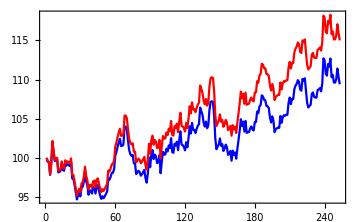

```mathematica
ListLinePlot[{px0,px05},Frame->True,AxesOrigin->{0,100},PlotStyle->{Blue,Red},ImageSize->Medium]
```

```mathematica
MCMultiPath[vec0_,vecμ_,vecσ_,matρ_,t_,steps_]:=Module[{dt,zeroμ,moves,paths},
dt=t/steps;
zeroμ=ConstantArray[0,Length[vec0]];
moves=Transpose[RandomVariate[MultinormalDistribution[zeroμ,matρ],steps]];
paths=MapThread[pricepath[#1,dt,#2]&,{Transpose[{vec0,vecμ,vecσ}],moves}];
paths];
MCMultiPath::"usage"="MCMultiPath[vec0,vecμ,vecσ,matρ,t,steps] returns correlated paths";
MCMultiPaths[vec0_,vecμ_,vecσ_,matρ_,t_,steps_,npaths_]:=Table[MCMultiPath[vec0,vecμ,vecσ,matρ,t,steps],{npaths}];
MCMultiPaths::"usage"="MCMultiPaths[vec0,vecμ,vecσ,matρ,t,steps,npaths] returns a table with npaths correlated MC paths";
MCMultiPathsLast[vec0_,vecμ_,vecσ_,matρ_,t_,npaths_]:=Table[Map[Last,MCMultiPath[vec0,vecμ,vecσ,matρ,t,1]],{npaths}];
MCMultiPathsLast::"usage"="MCMultiPathsLast[vec0,vecμ,vecσ,matρ,t,npaths] returns a table with the endpoints of npaths correlated MC paths";
MCMultiPathsPayoff[payoff_,vec0_,vecμ_,vecσ_,matρ_,t_,npaths_]:=Map[payoff,MCMultiPathsLast[vec0,vecμ,vecσ,matρ,t,npaths]];
MCMultiPathsPayoff::"usage"="MCMultiPathsLast[payoff,vec0,vecμ,vecσ,matρ,t,npaths] returns a table with a payoff applied to the endpoints of npaths correlated MC paths";
```

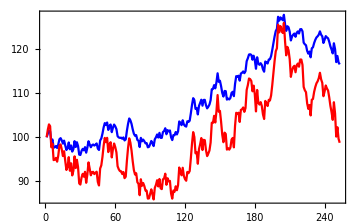

```mathematica
ListLinePlot[MCMultiPath[{100,100},{+0.10,-0.10},{0.15,0.30},{{1, +0.999}, {+0.999, 1}},1,252],Frame->True,AxesOrigin->{0,100},PlotStyle->{Blue,Red},ImageSize->Medium]
```

```mathematica
ListPointPlot3D[With[{vec0={1.26,0.7356,109.96},vecμ={0,0,0},vecσ={0.068,0.086,0.055},matρ={{1, -0.69, 0.13}, {-0.69, 1, -0.26}, {0.13, -0.26, 1}},t=1/4,npaths=1000},MCMultiPathsLast[vec0,vecμ,vecσ,matρ,t,npaths]],BoxRatios->{1, 1, 1},AxesLabel->{"CAD","AUD","JPY"}]
```

-Graphics3D-

```mathematica
SeedRandom[1234];TableForm[With[{vec0={1.26,0.7324,109.7},vecμ={0,0,0},vecσ={0.068,0.086,0.055},matρ={{1, -0.69, 0.13}, {-0.69, 1, -0.26}, {0.13, -0.26, 1}},t=1/4,npaths=10},MCMultiPathsLast[vec0,vecμ,vecσ,matρ,t,npaths]]]
```

1.23769 | 0.741212 | 104.982
1.37931 | 0.648694 | 108.47
1.26374 | 0.692451 | 110.998
1.29993 | 0.693628 | 110.35
1.2438 | 0.744013 | 108.989
1.28339 | 0.672888 | 111.454
1.221 | 0.728649 | 111.45
1.24009 | 0.76839 | 109.101
1.31529 | 0.678388 | 109.335
1.28334 | 0.720346 | 108.659

```mathematica
SeedRandom[1234];TableForm[With[{payoff=Min[{Max[(#[[1]]-1.26)/(#[[1]]),0],Max[0.7324-#[[2]],0],Max[(109.7-#[[3]])/(#[[3]]),0]}]&,vec0={1.26,0.7324,109.7},vecμ={0,0,0},vecσ={0.068,0.086,0.055},matρ={{1, -0.69, 0.13}, {-0.69, 1, -0.26}, {0.13, -0.26, 1}},t=1/4,npaths=10},MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,matρ,t,npaths]]]
```

0
0.0113404
0
0
0
0
0
0
0.00333378
0.00958332

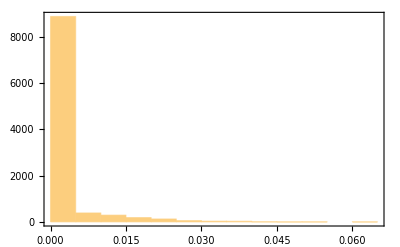

```mathematica
SeedRandom[1234];Histogram[With[{payoff=Min[{Max[(#[[1]]-1.26)/(#[[1]]),0],Max[0.7324-#[[2]],0],Max[(109.7-#[[3]])/(#[[3]]),0]}]&,vec0={1.26,0.7324,109.7},vecμ={0,0,0},vecσ={0.068,0.086,0.055},matρ={{1, -0.69, 0.13}, {-0.69, 1, -0.26}, {0.13, -0.26, 1}},t=1/4,npaths=10000},MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,matρ,t,npaths]],Frame->True]
```

```mathematica
SeedRandom[1234];With[{payoff=500 10^6 Min[{Max[(#[[1]]-1.26)/(#[[1]]),0],1/0.7324 Max[0.7324-#[[2]],0],Max[(109.7-#[[3]])/(#[[3]]),0]}]&,vec0={1.26,0.7324,109.7},vecμ={0,0,0},vecσ={0.069,0.086,0.055},matρ={{1, -0.69, 0.13}, {-0.69, 1, -0.26}, {0.13, -0.26, 1}},t=1/4,npaths=10000},Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,matρ,t,npaths]]]
```

975228.

```mathematica
500 1/0.7324 bspremium[-1,0.7324,0.7324,0,0,0.086,1/4]
```

8.5766

```mathematica
SeedRandom[1234];With[{payoff=500 10^6 Min[{∞,1/0.7324 Max[0.7324-#[[2]],0],∞}]&,vec0={1.26,0.7324,109.7},vecμ={0,0,0},vecσ={0.069,0.086,0.055},matρ={{1, -0.69, 0.13}, {-0.69, 1, -0.26}, {0.13, -0.26, 1}},t=1/4,npaths=10000},Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,matρ,t,npaths]]]
```

8.64715×10^6

```mathematica
SeedRandom[1234];With[{payoff=500 10^6 Min[{Max[(#[[1]]-1.26)/(#[[1]]),0],1/0.7324 Max[0.7324-#[[2]],0],∞}]&,vec0={1.26,0.7324,109.7},vecμ={0,0,0},vecσ={0.069,0.086,0.055},matρ={{1, -0.69, 0.13}, {-0.69, 1, -0.26}, {0.13, -0.26, 1}},t=1/4,npaths=10000},Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,matρ,t,npaths]]]
```

4.54803×10^6

```mathematica
SeedRandom[1234];With[{payoff=500 10^6 Min[{∞,1/0.7324 Max[0.7324-#[[2]],0],Max[(109.7-#[[3]])/(#[[3]]),0]}]&,vec0={1.26,0.7324,109.7},vecμ={0,0,0},vecσ={0.069,0.086,0.055},matρ={{1, -0.69, 0.13}, {-0.69, 1, -0.26}, {0.13, -0.26, 1}},t=1/4,npaths=10000},Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,matρ,t,npaths]]]
```

1.47243×10^6

```mathematica
SeedRandom[1234];With[{payoff=500 10^6 Min[{Max[(#[[1]]-1.26)/(#[[1]]),0],1/0.7324 Max[0.7324-#[[2]],0],Max[(109.7-#[[3]])/(#[[3]]),0]}]&,vec0={1.26,0.7324,109.7},vecμ={0,0,0},vecσ={0.068,0.086,0.055},matρ={{1, 0, 0}, {0, 1, 0}, {0, 0, 1}},t=1/4,npaths=10000},Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,matρ,t,npaths]]]
```

756753.

```mathematica
randcorrmat[n_]:=Module[{q},
q=RandomReal[{-1,1},{n,n}];
Rescale[Dot[Transpose[q],q],{-3,3},{-1,1}]];
```

```mathematica
Apply[And,Table[PositiveDefiniteMatrixQ[randcorrmat[3]],10000]]
```

True

```mathematica
pvs=With[{payoff=500 10^6 Min[{Max[(#[[1]]-1.26)/(#[[1]]),0],Max[0.7324-#[[2]],0],Max[(109.7-#[[3]])/(#[[3]]),0]}]&,vec0={1.26,0.7324,109.7},vecμ={0,0,0},vecσ={0.068,0.086,0.055},t=1/4,npaths=1000},Table[Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,randcorrmat[3],t,npaths]],1000]];
```

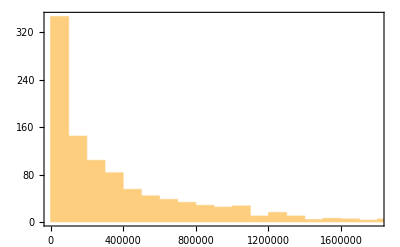

```mathematica
Histogram[pvs,Frame->True,AxesOrigin->{900000,0}]
```

```mathematica
DateDifference[{2021,9,1},{2022,1,18}]
```

139 days

```mathematica
SeedRandom[1234];With[{payoff=5 10^6 Boole[(#[[1]]>=1.23)&&(#[[2]]<=109)]&,vec0={1.1840,110.01},vecμ={0.008,0.004},vecσ={0.0555,0.057},matρ={{1, -0.36}, {-0.36, 1}},t=139/365,npaths=10000},Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,matρ,t,npaths]]]
```

447500

```mathematica
SeedRandom[1234];With[{payoff=5 10^6 Boole[(#[[1]]>=1.23)&&(#[[2]]<=109)]&,vec0={1.1840,110.01},vecμ={0.008,0.004},vecσ={0.0555,0.057},matρ={{1, 0}, {0, 1}},t=139/365,npaths=10000},Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,matρ,t,npaths]]]
```

282500

```mathematica
SeedRandom[1234];With[{payoff=5 10^6 Boole[(#[[1]]>=1.23)&&(#[[2]]>=109)]&,vec0={1.1840,110.01},vecμ={0.008,0.004},vecσ={0.0555,0.057},matρ={{1, -0.47}, {-0.47, 1}},t=139/365,npaths=10000},Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,matρ,t,npaths]]]
```

214000

```mathematica
SeedRandom[1234];With[{payoff=5 10^6 Boole[(#[[1]]>=1.23)]&,vec0={1.1840,110.01},vecμ={0.008,0.004},vecσ={0.0555,0.05744},matρ={{1, 0}, {0, 1}},t=139/365,npaths=10000},Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,matρ,t,npaths]]]
```

713500

```mathematica
SeedRandom[1234];With[{payoff=5 10^6 Boole[(#[[2]]<=109)]&,vec0={1.1840,110.01},vecμ={0.008,0.004},vecσ={0.0555,0.05744},matρ={{1, 0}, {0, 1}},t=139/365,npaths=10000},Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,matρ,t,npaths]]]
```

1978500

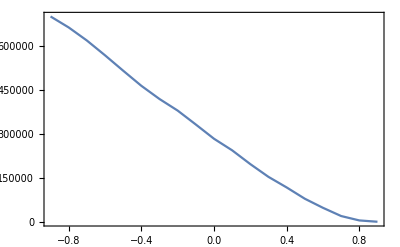

```mathematica
DiscretePlot[With[{payoff=5 10^6 Boole[(#[[1]]>=1.23)&&(#[[2]]<=109)]&,vec0={1.1840,110.01},vecμ={0.008,0.004},vecσ={0.0555,0.05744},t=139/365,npaths=10000},SeedRandom[1234];Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,{{1, ρ}, {ρ, 1}},t,npaths]]],{ρ,-0.9,+0.9,0.1},Frame->True,AxesOrigin->{0,0},Filling->None,Joined->True]
```

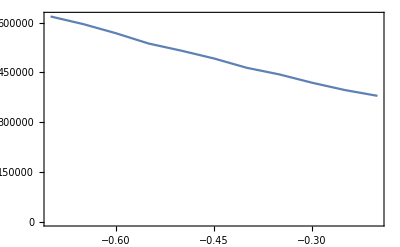

```mathematica
DiscretePlot[With[{payoff=5 10^6 Boole[(#[[1]]>=1.23)&&(#[[2]]<=109)]&,vec0={1.1840,110.01},vecμ={0.008,0.004},vecσ={0.0555,0.05744},t=139/365,npaths=10000},SeedRandom[1234];Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,{{1, ρ}, {ρ, 1}},t,npaths]]],{ρ,-0.7,-0.2,0.05},Frame->True,AxesOrigin->{-0.36,0},Filling->None,Joined->True]
```

```mathematica
SeedRandom[1234];With[{payoff=2 10^6 Boole[(#[[1]]<=19.55)]&,vec0={20},vecμ={0.05},vecσ={0.10},matρ={{1}},t=78/365,npaths=10000},Mean[MCMultiPathsPayoff[payoff,vec0,vecμ,vecσ,matρ,t,npaths]]]
```

488400

```mathematica
SeedRandom[1234];pricepath[{100,0,0.16},1/252,RandomVariate[NormalDistribution[],252]]
```

{100,99.4839,99.4081,97.8189,99.3406,102.053,100.703,99.5927,99.7313,99.831,98.1566,98.187,98.3506,99.2764,98.4475,98.3523,99.377,99.0085,99.1919,99.0508,98.962,99.5151,97.3658,97.3707,96.5341,95.6502,94.6857,95.1494,95.5121,95.0736,96.1679,96.3058,96.9691,98.2232,97.0262,96.4557,95.285,95.8165,95.838,95.4338,96.228,96.3177,95.4335,96.3837,96.5342,95.8178,95.1821,94.751,95.0965,94.8473,95.0821,95.3953,95.6935,97.3578,97.2081,97.5737,98.0786,98.1005,98.5355,100.245,100.773,101.393,101.989,102.424,101.515,101.53,101.713,104.002,103.995,103.607,102.149,100.964,100.462,100.251,100.373,99.3045,99.2633,97.9171,98.1742,98.3485,98.1739,97.7212,97.9058,98.1931,98.4727,97.4046,96.833,98.0062,100.033,98.8001,100.408,100.998,99.8471,100.413,100.186,99.3336,99.4423,100.355,98.0346,99.5138,100.771,100.433,100.424,101.166,100.808,101.586,101.249,102.509,100.731,100.648,101.808,101.583,102.072,100.988,102.263,103.379,101.721,101.627,101.383,100.96,101.997,101.342,102.535,104.028,103.109,104.469,103.583,103.561,103.179,103.693,104.098,104.307,106.418,105.968,105.482,104.47,103.99,104.629,103.787,104.158,106.125,107.158,107.233,107.135,105.492,102.515,101.095,101.415,101.733,102.476,101.544,101.757,100.879,101.181,101.691,101.373,100.377,100.581,100.872,99.6329,100.923,100.385,100.697,99.8937,101.171,102.301,103.497,104.935,104.081,104.623,103.359,104.723,103.198,103.263,103.298,103.777,104.012,103.63,103.497,104.578,104.58,105.916,105.705,106.585,106.746,107.989,107.844,107.402,107.362,106.636,106.577,106.373,105.179,104.525,105.3,104.742,103.286,103.63,103.778,103.875,103.831,105.35,104.473,105.198,105.447,105.374,105.503,105.491,107.019,107.704,106.87,107.528,107.503,108.782,109.22,109.452,109.931,109.689,108.725,108.581,110.093,109.851,110.172,108.551,107.015,106.437,106.627,106.783,108.165,108.364,107.787,107.708,107.695,108.668,108.749,108.911,108.5,109.506,112.711,112.458,110.756,110.507,111.997,111.66,112.691,110.311,110.612,109.627,109.614,110.042,111.408,110.375,109.402}

```mathematica
SeedRandom[1234];pricepath[{100,0,0.16},1/252,RandomVariate[StudentTDistribution[10000],252]]
```

{100,101.069,100.316,103.145,102.322,102.207,102.776,103.588,103.785,104.645,103.325,103.016,103.705,103.423,102.512,103.694,104.426,104.498,106.078,107.229,107.863,108.214,108.563,108.96,109.426,108.381,106.714,107.138,110.173,107.609,108.67,107.731,106.765,106.526,108.598,109.325,109.509,109.68,109.826,110.69,109.203,108.951,109.462,108.489,108.296,107.997,108.042,107.48,108.663,110.672,111.011,110.373,109.41,109.276,109.312,110.03,110.352,111.194,109.82,111.152,109.739,109.303,109.041,108.699,109.518,109.458,109.46,110.369,111.968,112.212,113.733,112.505,112.306,111.47,111.809,111.737,112.838,112.027,112.633,111.571,112.862,112.447,112.879,113.021,111.966,111.194,112.236,111.151,113.448,113.103,112.056,111.947,112.143,113.146,113.733,114.395,112.879,113.433,115.641,114.367,113.699,113.86,113.22,111.715,111.892,111.602,112.171,112.578,111.22,109.787,108.918,109.763,110.217,109.284,109.201,109.527,111.1,109.95,110.342,110.086,108.754,109.099,109.163,107.557,108.798,109.409,109.39,108.313,107.16,108.082,108.572,108.977,109.207,108.89,107.969,109.003,110.425,111.657,110.401,109.27,110.667,107.275,107.508,108.01,107.527,106.765,108.834,107.326,106.513,105.897,104.836,106.202,104.819,104.771,105.31,104.062,103.039,105.01,103.776,103.551,103.398,104.861,104.945,106.116,107.376,107.842,107.438,109.283,110.177,110.132,110.162,110.38,112.304,111.71,112.542,113.839,111.532,111.948,113.108,113.919,114.491,114.884,113.099,112.889,112.242,112.909,110.964,110.343,110.55,109.6,109.5,111.565,111.669,112.92,112.933,113.238,111.882,112.204,113.492,111.534,112.02,113.329,112.574,113.905,112.993,113.739,115.402,115.923,116.161,116.382,117.429,118.398,117.636,117.292,117.365,115.028,114.36,115.349,114.199,115.228,114.528,115.878,117.354,118.22,120.437,122.257,124.046,124.186,124.406,122.776,122.739,124.454,124.406,123.844,123.439,123.674,123.077,124.542,122.648,121.996,122.1,121.219,120.914,123.099,122.882,122.764,123.221,124.338,124.182,125.893,123.521,125.427,125.759}

```mathematica
realizedlogrets[path_]:=Log[Rest[path]/Most[path]];
realizedlogrets::"usage"="realizedlogret[path] returns the realized logreturns of a path";
realizedvariance[path_]:=Module[{lrets},
lrets=realizedlogrets[path];
252/(Length[path]-1)Dot[lrets,lrets]];
realizedvariance::"usage"="realizedvariance[path] returns the realized variance of a path";
```

```mathematica
MCStTPath[S0_,t_,steps_,μ_,σ_,λ_:10000]:=Module[{dt,moves,path},
dt=t/steps;
moves=RandomVariate[StudentTDistribution[λ],steps];
path=pricepath[{S0,μ,σ},dt,moves];
path];
MCStTPath::"usage"="MCStTPath[S0,t,steps,μ,σ,λ=10000] returns a StudentT path";
MCStTPaths[S0_,t_,steps_,npaths_,μ_,σ_,λ_:10000]:=Table[MCStTPath[S0,t,steps,μ,σ,λ],{npaths}];
MCStTPaths::"usage"="MCStTPaths[S0,t,steps,npaths,μ,σ,λ=10000] returns a table with npaths StudentT paths";
```

```mathematica
Clear[MCStTVariance]
```

```mathematica
MCStTLogRets[S0_,t_,steps_,npaths_,μ_,σ_,λ_:10000]:=Map[realizedlogrets,MCStTPaths[S0,t,steps,npaths,μ,σ,λ]];
MCStTLogRets::"usage"="MCStTLogRets[S0,t,steps,npaths,μ,σ,λ=10000] returns a table with the logreturns of npaths StudentT paths";
MCStTVariance[S0_,t_,steps_,npaths_,μ_,σ_,λ_:10000]:=Map[realizedvariance,MCStTPaths[S0,t,steps,npaths,μ,σ,λ]];
MCStTVariance::"usage"="MCStTVariance[S0,t,steps,npaths,μ,σ,λ=10000] returns a list with the realized variance of npaths StudentT paths";
```

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.16,λ=10000,t=1,steps=12,npaths=2},
MCStTPath[S0,t,steps,μ,σ,λ]]
```

{100,104.905,101.286,114.957,110.724,110.059,112.805,116.847,117.773,122.207,115.208,113.541,116.966}

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.16,λ=10000,t=1,steps=12,npaths=2},
MCStTPaths[S0,t,steps,npaths,μ,σ,λ]]
```

{{100,104.905,101.286,114.957,110.724,110.059,112.805,116.847,117.773,122.207,115.208,113.541,116.966},{100,98.6769,94.6753,99.7,102.883,103.121,110.368,115.868,118.943,120.625,122.316,124.279,126.628}}

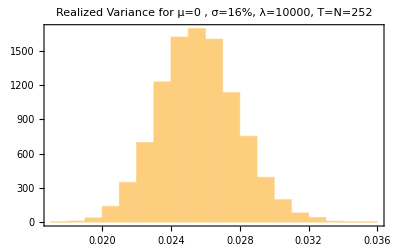

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.16,λ=10000,t=1,steps=252,npaths=10000},
Histogram[MCStTVariance[S0,t,steps,npaths,μ,σ,λ],
Frame->True,AxesOrigin->{σ^2,0},PlotLabel->"Realized Variance for μ=0 , σ=16%, λ=10000, T=N=252"]]
```

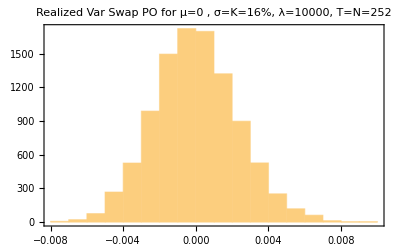

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.16,λ=10000,t=1,steps=252,npaths=10000,K=0.16},
Histogram[MCStTVariance[S0,t,steps,npaths,μ,σ,λ]-K^2,
Frame->True,AxesOrigin->{0,0},PlotLabel->"Realized Var Swap PO for μ=0 , σ=K=16%, λ=10000, T=N=252"]]
```

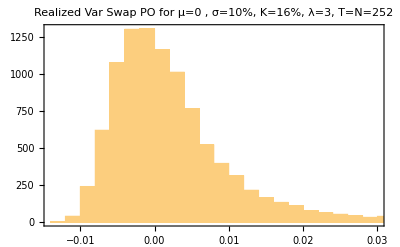

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.10,λ=3,t=1,steps=252,npaths=10000,K=0.16},
Histogram[MCStTVariance[S0,t,steps,npaths,μ,σ,λ]-K^2,
Frame->True,AxesOrigin->{0,0},PlotLabel->"Realized Var Swap PO for μ=0 , σ=10%, K=16%, λ=3, T=N=252"]]
```

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.092,λ=3,t=1,steps=252,npaths=10000,K=0.16},
Mean[MCStTVariance[S0,t,steps,npaths,μ,σ,λ]-K^2]]
```

-0.000276616

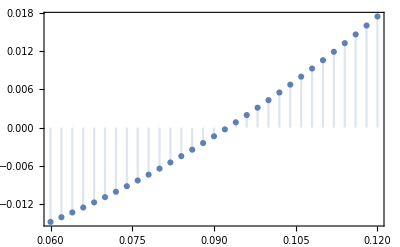

```mathematica
With[{S0=100,μ=0,λ=3,t=1,steps=252,npaths=10000,K=0.16},
DiscretePlot[Mean[SeedRandom[1234];MCStTVariance[S0,t,steps,npaths,μ,σ,λ]-K^2],{σ,0.06,0.12,0.002},Frame->True]]
```

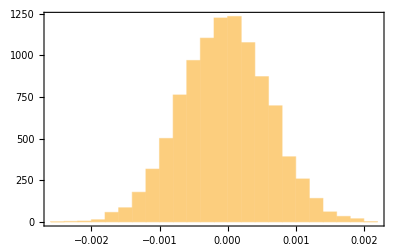

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.16,λ=10000,t=1,steps=252,npaths=10000},
Histogram[Map[Mean,MCStTLogRets[S0,t,steps,npaths,μ,σ,λ]],Frame->True,AxesOrigin->{0,0}]]
```

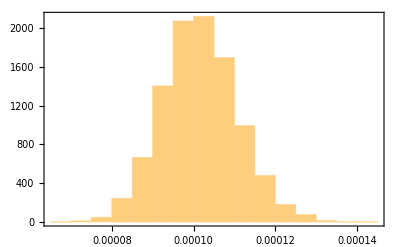

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.16,λ=10000,t=1,steps=252,npaths=10000},
Histogram[Map[Variance,MCStTLogRets[S0,t,steps,npaths,μ,σ,λ]],Frame->True,AxesOrigin->{0.0001,0}]]
```

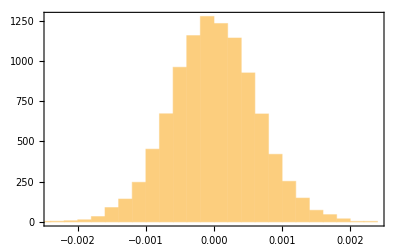

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.092,λ=3,t=1,steps=252,npaths=10000},
Histogram[Map[Mean,MCStTLogRets[S0,t,steps,npaths,μ,σ,λ]],Frame->True,AxesOrigin->{0,0}]]
```

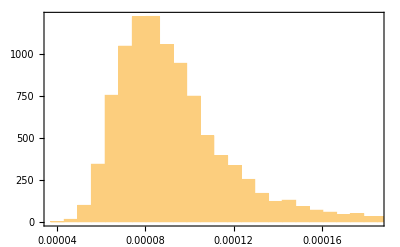

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.092,λ=3,t=1,steps=252,npaths=10000},
Histogram[Map[Variance,MCStTLogRets[S0,t,steps,npaths,μ,σ,λ]],Frame->True,AxesOrigin->{0.0001,0}]]
```

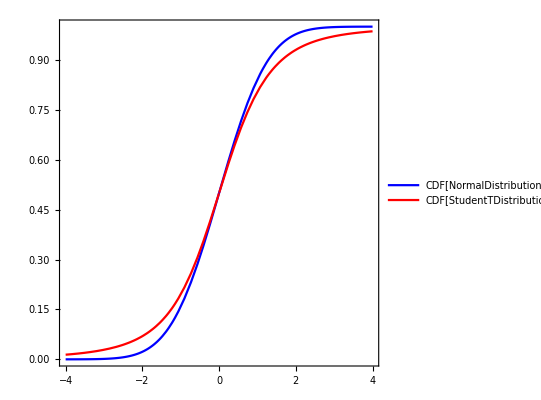

```mathematica
Plot[{CDF[NormalDistribution[],x],CDF[StudentTDistribution[3],x]},{x,-4,+4},Frame->True,PlotStyle->{Blue,Red},PlotLegends->"Expressions",AspectRatio->1]
```

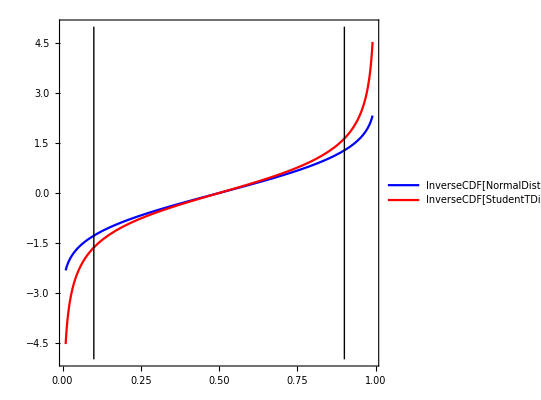

```mathematica
Show[Plot[{InverseCDF[NormalDistribution[],y],InverseCDF[StudentTDistribution[3],y]},{y,0.01,0.99},Frame->True,PlotStyle->{Blue,Red},PlotRange->All,PlotLegends->"Expressions",AspectRatio->1,AxesOrigin->{0.5,0}],Graphics[{Black,Line[{{0.1,-5},{0.1,+5}}]}],Graphics[{Black,Line[{{0.9,-5},{0.9,+5}}]}]]
```

```mathematica
Refine[{D[InverseCDF[NormalDistribution[],y],y],
D[InverseCDF[StudentTDistribution[3],y],y]},0<=y<=1]
```

{ⅇ^(InverseErfc[2 y]^2) √(2 π),Piecewise[{{(√3 π √(1-InverseBetaRegularized[2 y,3/2,1/2]))/(2 √(-1+1/InverseBetaRegularized[2 y,3/2,1/2]) InverseBetaRegularized[2 y,3/2,1/2]^(5/2)), 0<y<1/2}, {(√3 π)/2, y==1/2}, {(√3 π √(1-InverseBetaRegularized[2 (1-y),3/2,1/2]))/(2 √(-1+1/InverseBetaRegularized[2 (1-y),3/2,1/2]) InverseBetaRegularized[2 (1-y),3/2,1/2]^(5/2)), 1/2<y<1}, {Indeterminate, True}}]}

```mathematica
ⅇ^(InverseErfc[1]^2)
```

1

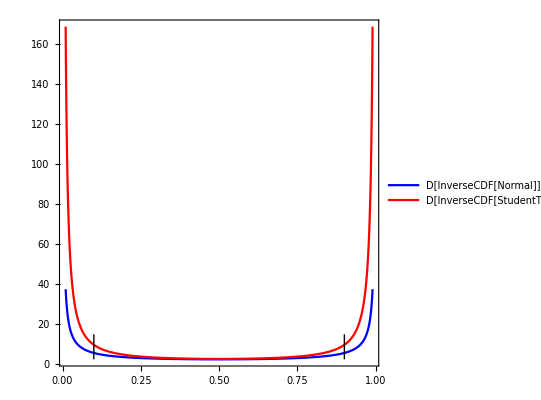

```mathematica
Show[Plot[{ⅇ^(InverseErfc[2 y]^2) √(2 π),Piecewise[{{(√3 π √(1-InverseBetaRegularized[2 y,3/2,1/2]))/(2 √(-1+1/InverseBetaRegularized[2 y,3/2,1/2]) InverseBetaRegularized[2 y,3/2,1/2]^(5/2)), 0<y<1/2}, {(√3 π)/2, y==1/2}, {(√3 π √(1-InverseBetaRegularized[2 (1-y),3/2,1/2]))/(2 √(-1+1/InverseBetaRegularized[2 (1-y),3/2,1/2]) InverseBetaRegularized[2 (1-y),3/2,1/2]^(5/2)), 1/2<y<1}, {Indeterminate, True}}]},{y,0.01,0.99},Frame->True,PlotStyle->{Blue,Red},PlotLegends->{"D[InverseCDF[Normal]]","D[InverseCDF[StudentT_3]]"},AspectRatio->1,AxesOrigin->{0.5,√(2 π)},PlotRange->All],Graphics[{Black,Line[{{0.1,√(2 π)},{0.1,+15}}]}],Graphics[{Black,Line[{{0.9,√(2 π)},{0.9,+15}}]}]]
```

```mathematica
gridStT[gridpoint_,datapoint_]:=PDF[StudentTDistribution[gridpoint[[1]],gridpoint[[2]],gridpoint[[3]]],datapoint];
```

```mathematica
distribStT[μgrid_,σgrid_,λgrid_,datapoint_]:=Map[gridStT[#,datapoint]&,Tuples[{μgrid,σgrid,λgrid}]];
```

```mathematica
posterior[μgrid_,σgrid_,λgrid_,priors_,datapoint_]:=Normalize[priors*distribStT[μgrid,σgrid,λgrid,datapoint],Total];
```

```mathematica
marginalsgrid[μgrid_,σgrid_,λgrid_,evals_]:=Module[{size,reshaped},
size=Map[Length,{μgrid,σgrid,λgrid}];
reshaped=ArrayReshape[evals,size];Chop[{Transpose[{μgrid,ArrayReduce[Total,reshaped,{2,3}]}],
Transpose[{σgrid,ArrayReduce[Total,reshaped,{1,3}]}],
Transpose[{λgrid,ArrayReduce[Total,reshaped,{1,2}]}]}]];
```

```mathematica
gridμ={-0.0025,-0.001,0,+0.001,0.0025};
gridσ={0.05,0.075,0.10,0.125,0.15,0.175,0.20}/16;
gridλ={2.1,3,4,5,10,100,1000,10000};
```

```mathematica
priorunif=Normalize[ConstantArray[1,Length[gridμ]*Length[gridσ]*Length[gridλ]],Total];
```

```mathematica
SeedRandom[1234];testpath1=With[{S0=100,μ=0,σ=0.15,λ=1000,t=1,steps=252,npaths=1},
MCStTLogRets[S0,t,steps,npaths,μ,σ,λ][[1]]];
```

```mathematica
updates1=FoldList[posterior[gridμ,gridσ,gridλ,#1,#2]&,priorunif,testpath1];
```

```mathematica
Map[Grid[#,Frame->All]&,marginalsgrid[gridμ,gridσ,gridλ,Last[updates1]]]
```

{-0.0025 | 7.64917×10^-8
-0.001 | 0.00521418
0 | 0.256298
0.001 | 0.722985
0.0025 | 0.0155036,0.003125 | 0
0.0046875 | 0
0.00625 | 1.5675×10^-6
0.0078125 | 0.0576621
0.009375 | 0.942074
0.0109375 | 0.000262258
0.0125 | 3.02507×10^-10,2.1 | 1.53401×10^-9
3 | 2.17886×10^-6
4 | 0.000213893
5 | 0.00233053
10 | 0.0499066
100 | 0.273604
1000 | 0.334029
10000 | 0.339914}

```mathematica
SeedRandom[1234];testpath1b=With[{S0=100,μ=0,σ=0.15,λ=3,t=1,steps=252,npaths=1},
MCStTLogRets[S0,t,steps,npaths,μ,σ,λ][[1]]];
```

```mathematica
updates1b=FoldList[posterior[gridμ,gridσ,gridλ,#1,#2]&,priorunif,testpath1b];
```

```mathematica
Map[Grid[#,Frame->All]&,marginalsgrid[gridμ,gridσ,gridλ,Last[updates1b]]]
```

{-0.0025 | 3.15446×10^-6
-0.001 | 0.00862237
0 | 0.200266
0.001 | 0.686149
0.0025 | 0.10496,0.003125 | 0
0.0046875 | 0
0.00625 | 0.0000114478
0.0078125 | 0.0715233
0.009375 | 0.835834
0.0109375 | 0.0923851
0.0125 | 0.000246395,2.1 | 0.0436074
3 | 0.45549
4 | 0.396651
5 | 0.104024
10 | 0.000227239
100 | 0
1000 | 0
10000 | 0}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates1[[10]]]]
```

{-0.0025 | 0.0580746
-0.001 | 0.121926
0 | 0.185163
0.001 | 0.261369
0.0025 | 0.373468,0.003125 | 0.00280401
0.0046875 | 0.046839
0.00625 | 0.148573
0.0078125 | 0.229427
0.009375 | 0.240991
0.0109375 | 0.195659
0.0125 | 0.135707,2.1 | 0.135158
3 | 0.159873
4 | 0.167417
5 | 0.167091
10 | 0.149943
100 | 0.112586
1000 | 0.107932}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates1[[50]]]]
```

{-0.0025 | 0.00354593
-0.001 | 0.0504622
0 | 0.175495
0.001 | 0.369426
0.0025 | 0.401071,0.003125 | 5.50329×10^-8
0.0046875 | 0.00184656
0.00625 | 0.105643
0.0078125 | 0.382958
0.009375 | 0.379326
0.0109375 | 0.117141
0.0125 | 0.0130852,2.1 | 0.0356901
3 | 0.0998437
4 | 0.155932
5 | 0.18905
10 | 0.214741
100 | 0.156721
1000 | 0.148023}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates1[[100]]]]
```

{-0.0025 | 0.000176496
-0.001 | 0.0291539
0 | 0.231525
0.001 | 0.549891
0.0025 | 0.189254,0.003125 | 0
0.0046875 | 0.0000109324
0.00625 | 0.038752
0.0078125 | 0.542146
0.009375 | 0.409945
0.0109375 | 0.00911549
0.0125 | 0.0000305086,2.1 | 0.0010765
3 | 0.0142972
4 | 0.0529033
5 | 0.109923
10 | 0.310018
100 | 0.263113
1000 | 0.248669}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates1[[150]]]]
```

{-0.0025 | 0.000439421
-0.001 | 0.110068
0 | 0.508232
0.001 | 0.372911
0.0025 | 0.00834928,0.003125 | 0
0.0046875 | 7.50473×10^-9
0.00625 | 0.00450177
0.0078125 | 0.48986
0.009375 | 0.502985
0.0109375 | 0.00265264
0.0125 | 6.66464×10^-7,2.1 | 0.0000321381
3 | 0.00190633
4 | 0.0201146
5 | 0.0752192
10 | 0.377778
100 | 0.269698
1000 | 0.255252}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates1[[200]]]]
```

{-0.0025 | 0.0000212784
-0.001 | 0.0447253
0 | 0.464246
0.001 | 0.483967
0.0025 | 0.00704024,0.003125 | 0
0.0046875 | 0
0.00625 | 0.0000767677
0.0078125 | 0.172504
0.009375 | 0.825952
0.0109375 | 0.00146701
0.0125 | 3.37839×10^-8,2.1 | 3.22267×10^-7
3 | 0.000087458
4 | 0.0027834
5 | 0.0170331
10 | 0.157831
100 | 0.393817
1000 | 0.428447}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,Last[updates1]]]
```

{-0.0025 | 7.80935×10^-8
-0.001 | 0.00517137
0 | 0.254869
0.001 | 0.724361
0.0025 | 0.0155987,0.003125 | 0
0.0046875 | 0
0.00625 | 2.37469×10^-6
0.0078125 | 0.0839763
0.009375 | 0.915784
0.0109375 | 0.000237141
0.0125 | 2.66845×10^-10,2.1 | 2.32396×10^-9
3 | 3.30088×10^-6
4 | 0.000324038
5 | 0.00353065
10 | 0.0756063
100 | 0.414497
1000 | 0.506039}

```mathematica
SeedRandom[1234];testpath2=With[{S0=100,μ=0,σ=0.09,λ=3,t=1,steps=252,npaths=1},
MCStTLogRets[S0,t,steps,npaths,μ,σ,λ][[1]]];
```

```mathematica
updates2=FoldList[posterior[gridμ,gridσ,gridλ,#1,#2]&,priorunif,testpath2];
```

```mathematica
updates2r=FoldList[posterior[gridμ,gridσ,gridλ,#1,#2]&,priorunif,Reverse[testpath2]];
```

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates2[[10]]]]
```

{-0.05 | 0
-0.025 | 7.80187×10^-9
0 | 0.999996
0.025 | 3.81386×10^-6
0.05 | 0,0.003125 | 0.0629894
0.0046875 | 0.240555
0.00625 | 0.261461
0.0078125 | 0.189226
0.009375 | 0.120762
0.0109375 | 0.0759601
0.0125 | 0.0490466,2.1 | 0.371519
3 | 0.273627
4 | 0.183174
5 | 0.12596
10 | 0.0367521
100 | 0.00510409
1000 | 0.00386374}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates2r[[10]]]]
```

{-0.05 | 0
-0.025 | 7.09831×10^-9
0 | 1.
0.025 | 9.66856×10^-8
0.05 | 0,0.003125 | 0.0532124
0.0046875 | 0.17122
0.00625 | 0.270802
0.0078125 | 0.241308
0.009375 | 0.148139
0.0109375 | 0.077225
0.0125 | 0.0380935,2.1 | 0.139878
3 | 0.145575
4 | 0.146307
5 | 0.146062
10 | 0.14393
100 | 0.139411
1000 | 0.138838}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates2[[50]]]]
```

{-0.05 | 0
-0.025 | 0
0 | 1.
0.025 | 0
0.05 | 0,0.003125 | 0.00193881
0.0046875 | 0.398557
0.00625 | 0.49203
0.0078125 | 0.0983178
0.009375 | 0.00855776
0.0109375 | 0.000560209
0.0125 | 0.0000388293,2.1 | 0.495691
3 | 0.302029
4 | 0.135684
5 | 0.0620819
10 | 0.00441289
100 | 0.0000643318
1000 | 0.0000370456}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates2r[[50]]]]
```

{-0.05 | 0
-0.025 | 0
0 | 1.
0.025 | 0
0.05 | 0,0.003125 | 0.000987834
0.0046875 | 0.173442
0.00625 | 0.518895
0.0078125 | 0.28517
0.009375 | 0.0209542
0.0109375 | 0.000541074
0.0125 | 9.9859×10^-6,2.1 | 0.0604784
3 | 0.118978
4 | 0.153611
5 | 0.174873
10 | 0.196791
100 | 0.150359
1000 | 0.14491}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates2[[100]]]]
```

{-0.05 | 0
-0.025 | 0
0 | 1.
0.025 | 0
0.05 | 0,0.003125 | 0.000124512
0.0046875 | 0.674032
0.00625 | 0.322478
0.0078125 | 0.00335898
0.009375 | 7.24503×10^-6
0.0109375 | 1.24484×10^-8
0.0125 | 0,2.1 | 0.420088
3 | 0.361442
4 | 0.151314
5 | 0.0662415
10 | 0.000913961
100 | 1.84385×10^-7
1000 | 5.52393×10^-8}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates2r[[100]]]]
```

{-0.05 | 0
-0.025 | 0
0 | 1.
0.025 | 0
0.05 | 0,0.003125 | 1.72081×10^-6
0.0046875 | 0.0588
0.00625 | 0.652771
0.0078125 | 0.284041
0.009375 | 0.00438035
0.0109375 | 5.21106×10^-6
0.0125 | 2.45748×10^-9,2.1 | 0.0235273
3 | 0.0817524
4 | 0.182863
5 | 0.266
10 | 0.226317
100 | 0.113767
1000 | 0.105773}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates2[[150]]]]
```

{-0.05 | 0
-0.025 | 0
0 | 1.
0.025 | 0
0.05 | 0,0.003125 | 3.63513×10^-7
0.0046875 | 0.587272
0.00625 | 0.412224
0.0078125 | 0.000503492
0.009375 | 3.89975×10^-8
0.0109375 | 0
0.0125 | 0,2.1 | 0.352839
3 | 0.374594
4 | 0.195424
5 | 0.077047
10 | 0.0000961911
100 | 0
1000 | 0}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates2r[[150]]]]
```

{-0.05 | 0
-0.025 | 0
0 | 1.
0.025 | 0
0.05 | 0,0.003125 | 1.83377×10^-9
0.0046875 | 0.0384105
0.00625 | 0.947105
0.0078125 | 0.0144806
0.009375 | 4.2859×10^-6
0.0109375 | 3.22213×10^-10
0.0125 | 0,2.1 | 0.0165613
3 | 0.116039
4 | 0.375163
5 | 0.452523
10 | 0.0397052
100 | 7.3046×10^-6
1000 | 4.43817×10^-7}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates2[[200]]]]
```

{-0.05 | 0
-0.025 | 0
0 | 1.
0.025 | 0
0.05 | 0,0.003125 | 6.07901×10^-10
0.0046875 | 0.263078
0.00625 | 0.736591
0.0078125 | 0.000330547
0.009375 | 3.54469×10^-9
0.0109375 | 0
0.0125 | 0,2.1 | 0.161957
3 | 0.283659
4 | 0.377101
5 | 0.177141
10 | 0.000141572
100 | 0
1000 | 0}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,updates2r[[200]]]]
```

{-0.05 | 0
-0.025 | 0
0 | 1.
0.025 | 0
0.05 | 0,0.003125 | 0
0.0046875 | 0.044161
0.00625 | 0.954426
0.0078125 | 0.00141346
0.009375 | 1.25234×10^-8
0.0109375 | 0
0.0125 | 0,2.1 | 0.00992157
3 | 0.0716774
4 | 0.341562
5 | 0.544448
10 | 0.0323907
100 | 5.30282×10^-7
1000 | 2.10221×10^-8}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,Last[updates2]]]
```

{-0.05 | 0
-0.025 | 0
0 | 1.
0.025 | 0
0.05 | 0,0.003125 | 0
0.0046875 | 0.124221
0.00625 | 0.875702
0.0078125 | 0.000076761
0.009375 | 0
0.0109375 | 0
0.0125 | 0,2.1 | 0.0621762
3 | 0.165375
4 | 0.464049
5 | 0.308164
10 | 0.000236505
100 | 0
1000 | 0}

```mathematica
Map[Grid,marginalsgrid[gridμ,gridσ,gridλ,Last[updates2r]]]
```

{-0.05 | 0
-0.025 | 0
0 | 1.
0.025 | 0
0.05 | 0,0.003125 | 0
0.0046875 | 0.124221
0.00625 | 0.875702
0.0078125 | 0.000076761
0.009375 | 0
0.0109375 | 0
0.0125 | 0,2.1 | 0.0621762
3 | 0.165375
4 | 0.464049
5 | 0.308164
10 | 0.000236505
100 | 0
1000 | 0}

### Variance Swap

bspremium[ϕ, S, K, r, q, σ, τ]

```mathematica
σskewK[K_,S0_,atm_,skew_]:=atm+(K-S0)*skew;
```

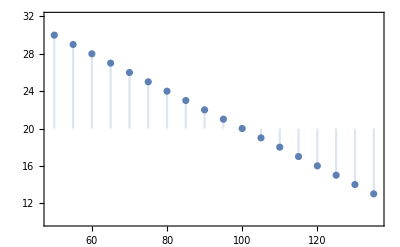

```mathematica
DiscretePlot[σskewK[K,100,20,-1/5],{K,50,135,5},Frame->True,AxesOrigin->{100,20},PlotRange->{{50-1,135+1},{10,32}}]
```

```mathematica
With[{S0=100,r=0.05,q=0,τ=90/365,σ=0.20,K=100},{bspremium[-1,S0,K,r,q,σ,τ],bspremium[+1,S0,K,r,q,σ,τ]}]
```

{3.35372,4.57903}

```mathematica
flogK[K_,S0_,τ_]:=2/τ((K-S0)/S0-Log[K/S0]);
```

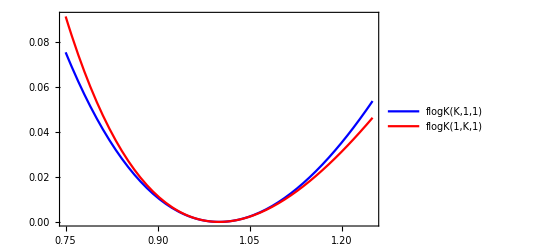

```mathematica
Plot[{flogK[K,1,1],flogK[1,K,1]},{K,0.75,1.25},
PlotRange->All,Frame->True,AxesOrigin->{1,0},
PlotStyle->{Blue,Red},PlotLegends->"Expressions"]
```

```mathematica
With[{S0=100,τ=90/365},flogK[100,S0,τ]]
```

0

```mathematica
D[2/τ((K-S0)/S0-Log[K/S0]),{K,2}]
```

2/(K^2 τ)

```mathematica
skewdelta[atm_,b_,δp_]:=atm+b(δp+1/2);
```

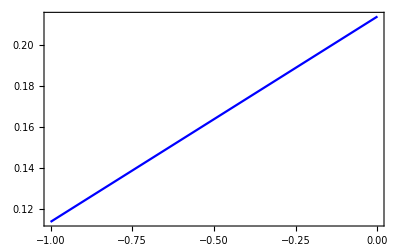

```mathematica
Plot[skewdelta[0.1638,0.1,δp],{δp,-1,0},
Frame->True,PlotRange->All,PlotStyle->Blue,AxesOrigin->{-0.5,0.1638}]
```

```mathematica
skew2delta[atm_,bc_,bp_,δ_]:=Piecewise[{{atm+bc(δ-1/2), δ≥0}, {atm+bp(δ+1/2), True}}];
```

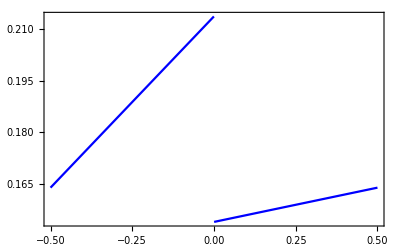

```mathematica
Plot[skew2delta[0.1638,0.02,0.1,δ],{δ,-0.5,+0.5},
Frame->True,PlotRange->All,PlotStyle->Blue,AxesOrigin->{-0.5,0.1638}]
```

```mathematica
kvarskew2[atm_,bc_,bp_,τ_]:=√(atm^2+atm((bp-bc)/4)+atm^2((bp+bc)/2)√(τ/π)+1/12(bp^2+bc^2)/2);
```

```mathematica
kvarskew2[0.0912,0,(0.015+0.003)/0.25,1]
```

0.101705

```mathematica
kvarskew2[0.1638,0.02,0.1,1/4]
```

0.176051

```mathematica
Plot3D[kvarskew2[atm,-bp/5,bp,1/4]-atm,{atm,0.12,0.30},{bp,0,0.5},AxesLabel->Automatic]
```

-Graphics3D-

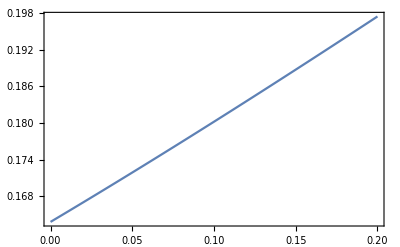

```mathematica
Plot[kvarskew2[0.1638,-bp/5,bp,1/4],{bp,0,0.2},Frame->True]
```

```mathematica
varswapNPO[size_,nexp_,Ksq_,lret_]:=size(252/nexp Total[lret^2]-Ksq);
```

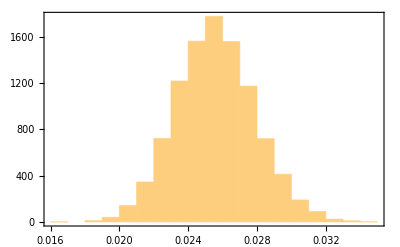

```mathematica
With[{σ=0.16,days=252,runs=10000},Histogram[Map[252/days Total[#]&,RandomVariate[NormalDistribution[0,σ/(√252)],{runs,days}]^2],AxesOrigin->{ σ^2,0},Frame->True]]
```

```mathematica
distvarswapNPO[size_,nexp_,Ksq_,dist_,runs_,days_]:=Map[varswapNPO[size,nexp,Ksq,#]&,RandomVariate[dist,{runs,days}]];
```

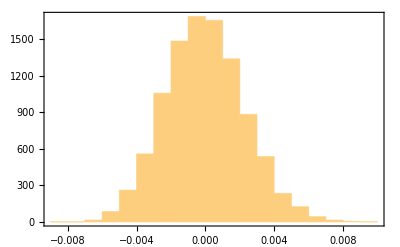

```mathematica
SeedRandom[1234];Histogram[distvarswapNPO[1,252,0.16^2,NormalDistribution[0,0.16/(√252)],10000,252],AxesOrigin->{ 0,0},Frame->True]
```

```mathematica
realizedvarswapPO[size_,nexp_,Ksq_,prices_]:=varswapNPO[size,nexp,Ksq,realizedlogrets[prices]];
```

```mathematica
realizedvarswapRV[size_,prices_]:=size realizedvariance[prices];
```

```mathematica
realizedvarswapLC[size_,prices_,Sref_,τ_]:=size flogK[Last[prices],Sref,τ];
```

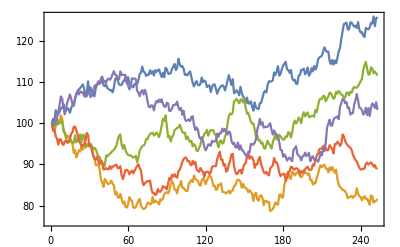

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.16,λ=10000,t=1,steps=252,npaths=5},
ListLinePlot[MCStTPaths[S0,t,steps,npaths,μ,σ,λ],Frame->True,PlotRange->All]]
```

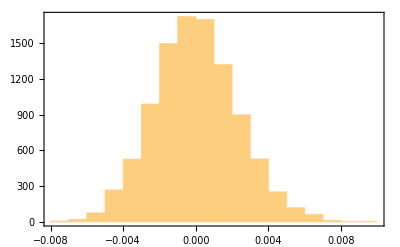

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.16,λ=10000,t=1,steps=252,npaths=10000,size=1,nexp=252,Ksq=0.16^2},
Histogram[Map[realizedvarswapPO[size,nexp,Ksq,#]&,MCStTPaths[S0,t,steps,npaths,μ,σ,λ]],Frame->True,AxesOrigin->{0,0}]]
```

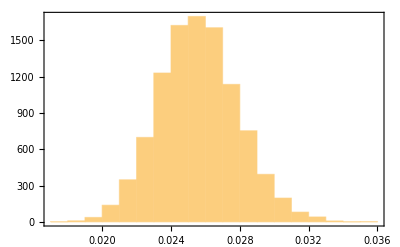

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.16,λ=10000,t=1,steps=252,npaths=10000,size=1,nexp=252,Ksq=0.16^2},
Histogram[Map[realizedvarswapRV[size,#]&,MCStTPaths[S0,t,steps,npaths,μ,σ,λ]],Frame->True,AxesOrigin->{0,0}]]
```

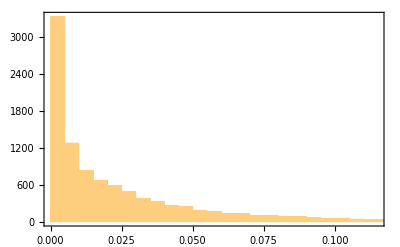

```mathematica
SeedRandom[1234];With[{S0=100,μ=0,σ=0.16,λ=10000,t=1,steps=252,npaths=10000,size=1,nexp=252,Ksq=0.16^2},
Histogram[Map[realizedvarswapLC[size,#,S0,t]&,MCStTPaths[S0,t,steps,npaths,μ,σ,λ]],Frame->True,AxesOrigin->{0,0}]]
```

```mathematica
realizedvarswapPOpieces[size_,nexp_,Ksq_,prices_]:=varswapNPO[size,nexp,Ksq,realizedlogrets[prices]];
```

```mathematica
wVarSwapK[size_,ϕ_,K1_,K2_,sumw_,S0_,atm_,skew_,τ_,r_,q_]:=Module[{neww,newsum,σcpK,optcpK,δcpK},
neww=size((flogK[K2,S0,τ]-flogK[K1,S0,τ])/(ϕ(K2-K1)))-sumw;
newsum=sumw+neww;
σcpK=σskewK[K1,S0,atm,skew];
optcpK=bspremium[ϕ,S0,K1,r,q,σcpK,τ];
δcpK=bsdelta[ϕ,S0,K1,r,q,σcpK,τ];
{ϕ,K1,K2,σcpK,neww,optcpK,δcpK,neww optcpK,newsum}];
```

```mathematica
TableForm[With[{S0=100,r=0.05,q=0,τ=90/365,atm=0.20,skew=-1/500,size=10000},
N[{wVarSwapK[size,+1,100,105,0,S0,atm,skew,τ,r,q],wVarSwapK[size,-1,100,95,0,S0,atm,skew,τ,r,q]}]]]
```

1. | 100. | 105. | 0.2 | 19.6262 | 4.57903 | 0.568988 | 89.8691 | 19.6262
-1. | 100. | 95. | 0.2 | 20.9801 | 3.35372 | -0.431012 | 70.3615 | 20.9801

```mathematica
wVarSwapKσ[inv_,size_,ϕ_,K1_,K2_,sumw_,S0_,σ_,τ_,r_,q_]:=Module[{iϕ,s0,k1,k2,rd,rf,neww,newsum,optcpK,δcpK},
If[inv,
iϕ=-ϕ;s0=1/S0;k1=1/K1;k2=1/K2;rd=q;rf=r;,
iϕ=ϕ;s0=S0;k1=K1;k2=K2;rd=r;rf=q;
];
neww=size  k1((flogK[k2,s0,τ]-flogK[k1,s0,τ])/(iϕ(k2-k1)))-sumw;
newsum=sumw+neww;
optcpK=If[inv,K1,1]bspremium[iϕ,s0,k1,rd,rf,σ,τ];
δcpK=If[inv,-K1/S0,1]bsdelta[iϕ,s0,k1,rd,rf,σ,τ];
{ϕ,K1,K2,σ,neww,optcpK,Log[K1/S0],δcpK,neww optcpK,newsum}];
```

```mathematica
TableForm[With[{S0=100,r=0.05,q=0,τ=90/365,atm=0.20,size=10000},
N[{wVarSwapKσ[False,size,+1,100,105,0,S0,atm,τ,r,q],wVarSwapKσ[False,size,-1,100,95,0,S0,atm,τ,r,q]}]]]
```

1. | 100. | 105. | 0.2 | 19.6262 | 4.57903 | 0. | 0.568988 | 89.8691 | 19.6262
-1. | 100. | 95. | 0.2 | 20.9801 | 3.35372 | 0. | -0.431012 | 70.3615 | 20.9801

```mathematica
TableForm[With[{S0=5.2640,r=0,q=0,τ=91/365,atm=0.1638,size=1},
N[{wVarSwapKσ[False,size,+1,S0,S0*(1+0.05),0,S0,atm,τ,r,q],wVarSwapKσ[False,size,-1,S0,S0*(1-0.05),0,S0,atm,τ,r,q]}]]]
```

1. | 5.264 | 5.5272 | 0.1638 | 0.0368742 | 0.171709 | 0. | 0.51631 | 0.00633162 | 0.0368742
-1. | 5.264 | 5.0008 | 0.1638 | 0.0394179 | 0.171709 | 0. | -0.48369 | 0.0067684 | 0.0394179

```mathematica
TableForm[With[{S0=5.2640,r=0,q=0,τ=91/365,atm=0.1638,size=1},
N[{wVarSwapKσ[True,size,+1,S0,S0*(1+0.05),0,S0,atm,τ,r,q],wVarSwapKσ[True,size,-1,S0,S0*(1-0.05),0,S0,atm,τ,r,q]}]]]
```

1. | 5.264 | 5.5272 | 0.1638 | 0.197288 | 0.0326195 | 0. | 0.48369 | 0.00643544 | 0.197288
-1. | 5.264 | 5.0008 | 0.1638 | 0.203978 | 0.0326195 | 0. | -0.51631 | 0.00665366 | 0.203978

```mathematica
{{bspremium[1,5.2640,5.2640,0,0,0.1638,91/365],bspremium[1,5.2640,5.2640,0,0,0.1638,91/365]/5.2640,5.2640bspremium[-1,1/5.2640,1/5.2640,0,0,0.1638,91/365]},
{bspremium[-1,5.2640,5.2640,0,0,0.1638,91/365],bspremium[-1,5.2640,5.2640,0,0,0.1638,91/365]/5.2640,5.2640bspremium[1,1/5.2640,1/5.2640,0,0,0.1638,91/365]}}
```

{{0.171709,0.0326195,0.0326195},{0.171709,0.0326195,0.0326195}}

```mathematica
TableForm[With[{S0=5.2640,r=0,q=0,τ=91/365,σ=0.2120,size=1},
N[{wVarSwapKσ[True,size,+1,6.5679,6.5679*(1+0.05),0,S0,σ,τ,r,q]}]]]
```

1. | 6.5679 | 6.8963 | 0.212 | 1.78986 | 0.000783964 | 0.221303 | 0.0200059 | 0.00140319 | 1.78986

```mathematica
{bspremium[1,5.2640,6.5679,0,0,0.2120,91/365],bspremium[1,5.2640,6.5679,0,0,0.2120,91/365]/5.2640,6.5679bspremium[-1,1/5.2640,1/6.5679,0,0,0.2120,91/365]}
```

{0.00412679,0.000783964,0.000783964}

```mathematica
bsdelta[1,5.2640,6.5679,0,0,0.2120,91/365]-bspremium[1,5.2640,6.5679,0,0,0.2120,91/365]/5.2640
```

0.0200059

```mathematica
6.5679/5.2640 bsdelta[-1,1/5.2640,1/6.5679,0,0,0.2120,91/365]
```

-0.0200059

```mathematica
wktbl[size_,S0_,KrngC_,KrngP_,atm_,skew_,τ_,r_,q_]:=Module[{wc0,wp0,wcks,wpks,wcpks},
wc0=wVarSwapK[size,+1,KrngC[[1]],KrngC[[2]],0,S0,atm,skew,τ,r,q];
wp0=wVarSwapK[size,-1,KrngP[[1]],KrngP[[2]],0,S0,atm,skew,τ,r,q];
wcks=FoldList[wVarSwapK[size,+1,#1[[3]],#2,Last[#1],S0,atm,skew,τ,r,q]&,wc0,Drop[KrngC,2]];
wpks=FoldList[wVarSwapK[size,-1,#1[[3]],#2,Last[#1],S0,atm,skew,τ,r,q]&,wp0,Drop[KrngP,2]];
wcpks=Join[Reverse[wpks],wcks];
wcpks=Map[Most,wcpks];
Map[Delete[#,3]&,wcpks]];
```

```mathematica
fvarK[size_,S0_,KrngC_,KrngP_,atm_,skew_,τ_,r_,q_]:=√Total[Last[Transpose[wktbl[size,S0,KrngC,KrngP,atm,skew,τ,r,q]]]];
```

```mathematica
varswaptable=With[{S0=100,r=0.05,q=0,τ=90/365,atm=0.20,skew=-1/500,size=10000,KrngP=Range[100,50-5,-5],KrngC=Range[100,135+5,5]},
wktbl[size,S0,KrngC,KrngP,atm,skew,τ,r,q]];
```

```mathematica
TableForm[N[varswaptable]]
```

-1. | 50. | 0.3 | 163.039 | 2.22841×10^-6 | -7.53875×10^-7 | 0.000363318
-1. | 55. | 0.29 | 134.625 | 0.0000257691 | -8.19367×10^-6 | 0.00346916
-1. | 60. | 0.28 | 113.047 | 0.000212943 | -0.0000635021 | 0.0240726
-1. | 65. | 0.27 | 96.2746 | 0.00133872 | -0.000373041 | 0.128884
-1. | 70. | 0.26 | 82.9783 | 0.00670006 | -0.00173513 | 0.555959
-1. | 75. | 0.25 | 72.2595 | 0.0275941 | -0.00659187 | 1.99393
-1. | 80. | 0.24 | 63.4921 | 0.095806 | -0.0209035 | 6.08293
-1. | 85. | 0.23 | 56.2296 | 0.285364 | -0.0561385 | 16.0459
-1. | 90. | 0.22 | 50.146 | 0.738365 | -0.128832 | 37.026
-1. | 95. | 0.21 | 44.9993 | 1.67473 | -0.253903 | 75.3616
-1. | 100. | 0.2 | 20.9801 | 3.35372 | -0.431012 | 70.3615
1. | 100. | 0.2 | 19.6262 | 4.57903 | 0.568988 | 89.8691
1. | 105. | 0.19 | 36.8269 | 2.25808 | 0.367197 | 83.158
1. | 110. | 0.18 | 33.5517 | 0.887442 | 0.188428 | 29.7752
1. | 115. | 0.17 | 30.6948 | 0.257795 | 0.0711362 | 7.91298
1. | 120. | 0.16 | 28.1881 | 0.0500871 | 0.0178692 | 1.41186
1. | 125. | 0.15 | 25.9763 | 0.00568388 | 0.00261049 | 0.147646
1. | 130. | 0.14 | 24.0151 | 0.000312154 | 0.000184093 | 0.00749642
1. | 135. | 0.13 | 22.268 | 6.34883×10^-6 | 4.80688×10^-6 | 0.000141376

```mathematica
fvarK[10000,100,Range[100,135+5,5],Range[100,50-5,-5],0.20,-1/500,90/365,0.05,0]
```

20.4907

```mathematica
Clear[wktblσ]
```

```mathematica
wktblσ[inv_,size_,S0_,KσrngC_,KσrngP_,τ_,r_,q_]:=Module[{KrngC,σrngC,KrngP,σrngP,wc0,wp0,foldc,foldp,wcks,wpks,wcpks},
{KrngC,σrngC}=Transpose[KσrngC];
{KrngP,σrngP}=Transpose[KσrngP];
wc0=wVarSwapKσ[inv,size,+1,KrngC[[1]],KrngC[[2]],0,S0,σrngC[[1]],τ,r,q];
wp0=wVarSwapKσ[inv,size,-1,KrngP[[1]],KrngP[[2]],0,S0,σrngP[[1]],τ,r,q];
foldc=Transpose[{Drop[KrngC,2],Most[Rest[σrngC]]}];
foldp=Transpose[{Drop[KrngP,2],Most[Rest[σrngP]]}];
wcks=FoldList[wVarSwapKσ[inv,size,+1,#1[[3]],#2[[1]],Last[#1],S0,#2[[2]],τ,r,q]&,wc0,foldc];
wpks=FoldList[wVarSwapKσ[inv,size,-1,#1[[3]],#2[[1]],Last[#1],S0,#2[[2]],τ,r,q]&,wp0,foldp];
wcpks=Join[Reverse[wpks],wcks];
wcpks=Map[Most,wcpks];
Map[Delete[#,3]&,wcpks]];
```

```mathematica
fvarKσ[inv_,size_,S0_,KσrngC_,KσrngP_,τ_,r_,q_]:=√Total[Last[Transpose[wktblσ[inv,size,S0,KσrngC,KσrngP,τ,r,q]]]];
```

```mathematica
DateDifference[{2021,8,30},{2021,11,29}]
```

91 days

{ϕ,K1,K2,σ,neww,optcpK,Log[K1/S0],δcpK,neww optcpK,newsum}

```mathematica
TableForm[With[{S0=5.2640,r=0,q=0,τ=91/365,atm=0.1638,size=1},
N[{wVarSwapKσ[True,size,+1,S0,S0*(1+0.06),0,S0,atm,τ,r,q],wVarSwapKσ[True,size,-1,S0,S0*(1-0.052),0,S0,atm,τ,r,q]}]]]
```

1. | 5.264 | 5.57984 | 0.1638 | 0.235986 | 0.0326195 | 0. | 0.48369 | 0.00769773 | 0.235986
-1. | 5.264 | 4.99027 | 0.1638 | 0.212284 | 0.0326195 | 0. | -0.51631 | 0.00692459 | 0.212284

```mathematica
TableForm[With[{S0=5.2640,r=0,q=0,τ=91/365,σ=0.2120,size=1},
N[{wVarSwapKσ[True,size,+1,6.5679,6.5679*(1+0.05),0,S0,σ,τ,r,q]}]]]
```

1. | 6.5679 | 6.8963 | 0.212 | 1.78986 | 0.000783964 | 0.221303 | 0.0200059 | 0.00140319 | 1.78986

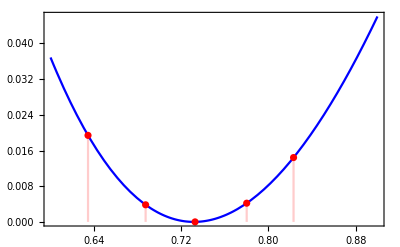

```mathematica
Show[Plot[flogK[K,0.7316,1],{K,0.6,0.9},
Frame->True,PlotRange->All,PlotStyle->Blue,AxesOrigin->{0.7316,0}],
DiscretePlot[flogK[K,0.7316,1],{K,{0.6344,0.68725,0.73262,0.78,0.823}},
Frame->True,PlotRange->All,PlotStyle->Red,AxesOrigin->{0.7316,0}]]
```

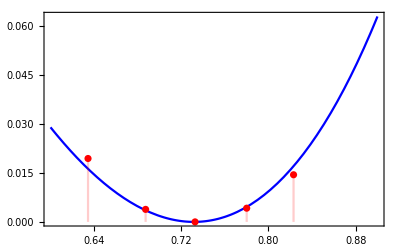

```mathematica
Show[Plot[flogK[2 0.7316-K,0.7316,1],{K,0.6,0.9},
Frame->True,PlotRange->All,PlotStyle->Blue,AxesOrigin->{0.7316,0}],
DiscretePlot[flogK[K,0.7316,1],{K,{0.6344,0.68725,0.73262,0.78,0.823}},
Frame->True,PlotRange->All,PlotStyle->Red,AxesOrigin->{0.7316,0}]]
```

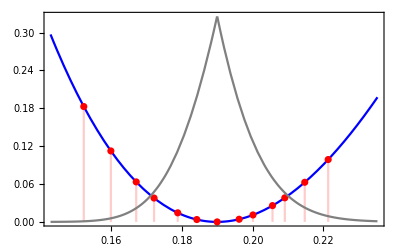

```mathematica
Show[Plot[flogK[K,1/5.2640,91/365],{K,1/7,1/4.25},
Frame->True,PlotRange->All,PlotStyle->Blue,AxesOrigin->{1/5.2640,0}],
DiscretePlot[flogK[K,1/5.2640,91/365],{K,1/{6.5679,6.2533,5.9851,5.8098,5.5922,5.4283,5.2640,5.0972,4.9976,4.8633,4.7824,4.6569,4.5175}},
Frame->True,PlotRange->All,PlotStyle->Red,AxesOrigin->{1/5.2640,0}],
Plot[10/K bspremium[If[K>1/5.2640,+1,-1],1/5.2640,K,0,0,0.1638,91/365],{K,1/7,1/4.25},
Frame->True,PlotRange->All,PlotStyle->Gray,AxesOrigin->{1/5.2640,0}]]
```

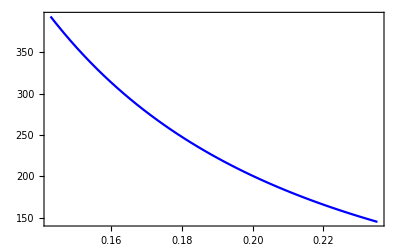

```mathematica
Plot[2/(K^2 91/365),{K,1/7,1/4.25},
Frame->True,PlotRange->All,PlotStyle->Blue,AxesOrigin->{1/5.2640,0}]
```

```mathematica
Clear[varswaptableBRL]
```

```mathematica
varswaptableBRL=With[{S0=5.2640,r=0,q=0,τ=91/365,size=1,
KrngC=Reverse[{{7, 0.2120}, {6.5679, 0.2120}, {6.2533, 0.2059}, {5.9851, 0.1972}, {5.8098, 0.1899}, {5.5922, 0.1791}, {5.4283, 0.1714}, {5.2640, 0.1638}}],KrngP={{5.2640, 0.1638}, {5.0972, 0.1578}, {4.9976, 0.1549}, {4.8633, 0.1528}, {4.7824, 0.1520}, {4.6569, 0.1513}, {4.5175, 0.1511}, {4.4, 0.1511}}},
wktblσ[True,size,S0,KrngC,KrngP,τ,r,q]];
```

{ϕ,K1,σ,neww,optcpK,Log[K1/S0],δcpK,neww optcpK}

```mathematica
TableForm[Prepend[N[varswaptableBRL],{ϕ,K,σ,neww,optcpK,Log[K/S0],δcpK,neww optcpK}]]
```

ϕ | K | σ | neww | optcpK | Log[K/S0] | δcpK | neww optcpK
-1. | 4.5175 | 0.1511 | 0.263772 | 0.000551495 | -0.152932 | -0.0200245 | 0.000145469
-1. | 4.6569 | 0.1513 | 0.253049 | 0.00156663 | -0.122541 | -0.0500399 | 0.000396435
-1. | 4.7824 | 0.152 | 0.185977 | 0.00355042 | -0.0959487 | -0.0999807 | 0.000660295
-1. | 4.8633 | 0.1528 | 0.191665 | 0.00568068 | -0.079174 | -0.146671 | 0.00108879
-1. | 4.9976 | 0.1549 | 0.194981 | 0.0112929 | -0.0519334 | -0.250104 | 0.0022019
-1. | 5.0972 | 0.1578 | 0.212941 | 0.0176296 | -0.0321998 | -0.344683 | 0.00375406
-1. | 5.264 | 0.1638 | 0.12846 | 0.0326195 | 0. | -0.51631 | 0.0041903
1. | 5.264 | 0.1638 | 0.123908 | 0.0326195 | 0. | 0.48369 | 0.00404183
1. | 5.4283 | 0.1714 | 0.238801 | 0.0212688 | 0.0307348 | 0.354606 | 0.00507901
1. | 5.5922 | 0.1791 | 0.262179 | 0.0136982 | 0.0604816 | 0.250123 | 0.00359137
1. | 5.8098 | 0.1899 | 0.248559 | 0.00767409 | 0.098655 | 0.152672 | 0.00190747
1. | 5.9851 | 0.1972 | 0.270172 | 0.00473729 | 0.128382 | 0.100074 | 0.00127988
1. | 6.2533 | 0.2059 | 0.323982 | 0.00217458 | 0.172218 | 0.0500427 | 0.000704524
1. | 6.5679 | 0.212 | 0.383248 | 0.000783964 | 0.221303 | 0.0200059 | 0.000300453

```mathematica
fvarKσ[True,1,5.2640,Reverse[{{7, 0.2120}, {6.5679, 0.2120}, {6.2533, 0.2059}, {5.9851, 0.1972}, {5.8098, 0.1899}, {5.5922, 0.1791}, {5.4283, 0.1714}, {5.2640, 0.1638}}],{{5.2640, 0.1638}, {5.0972, 0.1578}, {4.9976, 0.1549}, {4.8633, 0.1528}, {4.7824, 0.1520}, {4.6569, 0.1513}, {4.5175, 0.1511}, {4.4, 0.1511}},91/365,0,0]
```

0.171294

```mathematica
TableForm[Prepend[N[With[{S0=5.2640,r=0,q=0,τ=91/365,size=1,
KrngC=Reverse[{{7, 0.2120}, {6.5679, 0.2120}, {6.2533, 0.2059}, {5.9851, 0.1972}, {5.5922, 0.1791}, {5.2640, 0.1638}}],KrngP={{5.2640, 0.1638}, {4.9976, 0.1549}, {4.7824, 0.1520}, {4.6569, 0.1513}, {4.5175, 0.1511}, {4.4, 0.1511}}},
wktblσ[True,size,S0,KrngC,KrngP,τ,r,q]]],{ϕ,K,σ,neww,optcpK,Log[K/S0],δcpK,neww optcpK}]]
```

ϕ | K | σ | neww | optcpK | Log[K/S0] | δcpK | neww optcpK
-1. | 4.5175 | 0.1511 | 0.263772 | 0.000551495 | -0.152932 | -0.0200245 | 0.000145469
-1. | 4.6569 | 0.1513 | 0.253049 | 0.00156663 | -0.122541 | -0.0500399 | 0.000396435
-1. | 4.7824 | 0.152 | 0.311157 | 0.00355042 | -0.0959487 | -0.0999807 | 0.00110474
-1. | 4.9976 | 0.1549 | 0.396365 | 0.0112929 | -0.0519334 | -0.250104 | 0.00447611
-1. | 5.264 | 0.1638 | 0.206501 | 0.0326195 | 0. | -0.51631 | 0.00673597
1. | 5.264 | 0.1638 | 0.245036 | 0.0326195 | 0. | 0.48369 | 0.00799296
1. | 5.5922 | 0.1791 | 0.501194 | 0.0136982 | 0.0604816 | 0.250123 | 0.00686543
1. | 5.9851 | 0.1972 | 0.39739 | 0.00473729 | 0.128382 | 0.100074 | 0.00188255
1. | 6.2533 | 0.2059 | 0.323982 | 0.00217458 | 0.172218 | 0.0500427 | 0.000704524
1. | 6.5679 | 0.212 | 0.383248 | 0.000783964 | 0.221303 | 0.0200059 | 0.000300453

```mathematica
fvarKσ[True,1,5.2640,Reverse[{{7, 0.2120}, {6.5679, 0.2120}, {6.2533, 0.2059}, {5.9851, 0.1972}, {5.5922, 0.1791}, {5.2640, 0.1638}}],{{5.2640, 0.1638}, {4.9976, 0.1549}, {4.7824, 0.1520}, {4.6569, 0.1513}, {4.5175, 0.1511}, {4.4, 0.1511}},91/365,0,0]
```

0.174942

```mathematica
fvarKσ[True,1,5.2640,Reverse[{{6.5679, 0.2120}, {6.2533, 0.2059}, {5.9851, 0.1972}, {5.5922, 0.1791}, {5.2640, 0.1638}}],{{5.2640, 0.1638}, {4.9976, 0.1549}, {4.7824, 0.1520}, {4.6569, 0.1513}, {4.5175, 0.1511}},91/365,0,0]
```

0.173663

```mathematica
fvarKσ[True,1,5.2640,Reverse[{{6.2533, 0.2059}, {5.9851, 0.1972}, {5.5922, 0.1791}, {5.2640, 0.1638}}],{{5.2640, 0.1638}, {4.9976, 0.1549}, {4.7824, 0.1520}, {4.6569, 0.1513}},91/365,0,0]
```

0.170463

```mathematica
fvarKσ[True,1,5.2640,Reverse[{{5.9851, 0.1972}, {5.5922, 0.1791}, {5.2640, 0.1638}}],{{5.2640, 0.1638}, {4.9976, 0.1549}, {4.7824, 0.1520}},91/365,0,0]
```

0.161464

```mathematica
varswaptableAUD=With[{S0=0.7316,r=0.0015,q=0.00016,τ=1,size=200000,
KrngC=Reverse[{{5.8098, 0.1899}, {5.5922, 0.1791}, {5.4283, 0.1714}, {5.2640, 0.1638}}],KrngP={{5.2640, 0.1638}, {5.0972, 0.1578}, {4.9976, 0.1549}, {4.8633, 0.1528}}},
wktblσ[False,size,S0,KrngC,KrngP,τ,r,q]];
```

### Correlation

```mathematica
ρikij[σik_,σij_,σjk_,sign_:+1]:=sign(σik^2+σij^2-σjk^2)/(2σik σij);
```